```mathematica
Light Scattering by a Spherical Particle for Mathematica 8
```

8 a by for Light Mathematica Particle Scattering Spherical

## Usage Notes

Date: 		Last Modification: 05/17/12
		Mathematica Version 8.0.10
		
Author:	Guy Mongelli
	  
	  	University of Rochester
	  	Dept. of Chemical Engineering
	  	Rochester, NY 14627
	  	mongelli@che.rochester.edu

Application:
	This notebook calculates and plots the scattering, absorption, and extinction properties of a spherical particle of known refractive index in a suspending medium, also of known index.  The particle is illuminated by an unpolarized or linearly polarized  plane wave of unit amplitude.  The code derives from expositions of the problem in Principles of Optics by Born and Wolf, Absorption and Scattering of Light by Small Particles by Bohren and Huffman, and Light Scattering by Small Particles  by H.C. van de Hulst.  It is capable of calculating the spectral properties of such a particle if the dispersion of both the particle and suspending medium are known.  Similarly, absorptive suspending media are allowable when the complex refractive index is provided.

Layout:
	Parameters such as cross sections, phase functions, efficiency factors, etc. may be calculated and displayed.

```mathematica
This code was altered further to consider a single material in various external refractive index media.  The code was essentially copied several times and the code was rerun with a greek letter designation added the the variables (α,β,γ,δ,ϵ)corresponding to each external refractive index.
```

## Model Parameters

This section is devoted to entering the known parameters for the problem (i.e., complex indices of refraction, wavelength of the illuminating radiation, sphere radius, etc.).  Subscripts of 1 correspond to the embedding medium and subscripts of 2 represent the sphere.  It is assumed by H.C. van de Hulst that neither the medium nor the particle is magnetic (or at very least they have the same permeability).  Notice that the imaginary part of the refractive index is represented by a lower case k, and that capital K represents the wave number.  Finally, it would be more efficient to assign the parameter values (lambda of excitation, radius, real and imaginary index) using rewrite rules in the actual function calls but I've presented them as constants because this format is more readable.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Define parameters for next=1.9
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.9

```mathematica
Subscript[n, 1α]= 1.9;                             (* Real part of refractive index of medium *)
Subscript[n, 2α]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1α] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2α]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0α] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, α]=.1                       (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.8
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.8

```mathematica
Subscript[n, 1β]= 1.8;                             (* Real part of refractive index of medium *)
Subscript[n, 2β]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1β] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2β]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0β] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, β]=.1                       (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.7
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.7

```mathematica
Subscript[n, 1γ]= 1.7;                             (* Real part of refractive index of medium *)
Subscript[n, 2γ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1γ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2γ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0γ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, γ]=.1                   (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.6
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.6

```mathematica
Subscript[n, 1δ]= 1.6;                             (* Real part of refractive index of medium *)
Subscript[n, 2δ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1δ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2δ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0δ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, δ]=.1                     (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.5
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.5

```mathematica
Subscript[n, 1ν]= 1.5;                             (* Real part of refractive index of medium *)
Subscript[n, 2ν]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1ν] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2ν]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0ν] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, ν]=.1                  (*Sphere radius in μm *);
```

```mathematica
Attempting a second function for next=1.5 due to an error in the code
```

Set::write: Tag Times in a\ Attempting\ for\ function\ next\ second is Protected.

1.5 an code due error in the to

```mathematica
Subscript[n, 1χ]= 1.5;                             (* Real part of refractive index of medium *)
Subscript[n, 2χ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1χ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
 Subscript[k, 2  χ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
 Subscript[λ, 0  χ] = 544543 *  10^-6;   (* Vacuum wavelength in μm *)
 Subscript[r, χ]=.1                   (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.4
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.4

```mathematica
Subscript[n, 1ζ]= 1.4;                             (* Real part of refractive index of medium *)
Subscript[n, 2ζ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1ζ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2ζ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0ζ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, ζ]=.1                (*Sphere radius in μm *);
```

```mathematica
Define paramaters for next=1.3
```

Set::write: Tag Times in Define\ for\ next\ paramaters is Protected.

1.3

```mathematica
Subscript[n, 1η]= 1.3;                             (* Real part of refractive index of medium *)
Subscript[n, 2η]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1η] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2η]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0η] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, η]=.1       (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.2
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.2

```mathematica
Subscript[n, 1θ]= 1.2;                             (* Real part of refractive index of medium *)
Subscript[n, 2θ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1θ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2θ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0θ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, θ]=.1           (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.1
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.1

```mathematica
Subscript[n, 1κ]= 1.1;                             (* Real part of refractive index of medium *)
Subscript[n, 2κ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1κ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2κ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0κ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, κ]=.1        (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.0
```

Set::write: Tag Times in Define\ for\ next\ parameters is Protected.

1.

```mathematica
Subscript[n, 1μ]= 1.0;                             (* Real part of refractive index of medium *)
Subscript[n, 2μ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1μ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2μ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0μ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, μ]=.1           (*Sphere radius in μm *);
```

Required derived quantities for given parameter set.

```mathematica
Subscript[m, 1α] = Subscript[n, 1α] + I Subscript[k, 1α];               (* Complex refractive index of medium *)
Subscript[m, 2α] = Subscript[n, 2α] + I Subscript[k, 2α];             (* Complex refractive index of scatterer *)
Subscript[m, Relα]= (Subscript[n, 2α] + I Subscript[k, 2α])/(Subscript[n, 1α] + I Subscript[k, 1α]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1α]=Subscript[λ, 0 α]/(Subscript[n, 1α] + I Subscript[k, 1α]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2α]=Subscript[λ, 0 α]/(Subscript[n, 2α] + I Subscript[k, 2α]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0α] =  (2 π)/Subscript[λ, 0α];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1α] =  (2 π)/Subscript[λ, 1α];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2α]=  (2 π)/Subscript[λ, 2α]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1β] = Subscript[n, 1β] + I Subscript[k, 1β];               (* Complex refractive index of medium *)
Subscript[m, 2β] = Subscript[n, 2β] + I Subscript[k, 2β];             (* Complex refractive index of scatterer *)
Subscript[m, Relβ]= (Subscript[n, 2β] + I Subscript[k, 2β])/(Subscript[n, 1β] + I Subscript[k, 1β]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1β]=Subscript[λ, 0 β]/(Subscript[n, 1β] + I Subscript[k, 1β]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2β]=Subscript[λ, 0 β]/(Subscript[n, 2β] + I Subscript[k, 2β]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0β] =  (2 π)/Subscript[λ, 0β];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1β] =  (2 π)/Subscript[λ, 1β];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2β]=  (2 π)/Subscript[λ, 2β]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1γ] = Subscript[n, 1γ] + I Subscript[k, 1γ];               (* Complex refractive index of medium *)
Subscript[m, 2γ] = Subscript[n, 2γ] + I Subscript[k, 2γ];             (* Complex refractive index of scatterer *)
Subscript[m, Relγ]= (Subscript[n, 2γ] + I Subscript[k, 2γ])/(Subscript[n, 1γ] + I Subscript[k, 1γ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1γ]=Subscript[λ, 0 γ]/(Subscript[n, 1γ] + I Subscript[k, 1γ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2γ]=Subscript[λ, 0γ]/(Subscript[n, 2γ] + I Subscript[k, 2γ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0γ] =  (2 π)/Subscript[λ, 0γ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1γ] =  (2 π)/Subscript[λ, 1γ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2γ]=  (2 π)/Subscript[λ, 2γ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1δ] = Subscript[n, 1δ] + I Subscript[k, 1δ];               (* Complex refractive index of medium *)
Subscript[m, 2δ] = Subscript[n, 2δ] + I Subscript[k, 2δ];             (* Complex refractive index of scatterer *)
Subscript[m, Relδ]= (Subscript[n, 2δ] + I Subscript[k, 2δ])/(Subscript[n, 1δ] + I Subscript[k, 1δ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1δ]=Subscript[λ, 0 δ]/(Subscript[n, 1δ] + I Subscript[k, 1δ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2δ]=Subscript[λ, 0δ]/(Subscript[n, 2δ] + I Subscript[k, 2δ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0δ] =  (2 π)/Subscript[λ, 0δ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1δ] =  (2 π)/Subscript[λ, 1δ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2δ]=  (2 π)/Subscript[λ, 2δ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1ν] = Subscript[n, 1ν] + I Subscript[k, 1ν];               (* Complex refractive index of medium *)
Subscript[m, 2ν] = Subscript[n, 2ν] + I Subscript[k, 2ν];             (* Complex refractive index of scatterer *)
Subscript[m, Relν]= (Subscript[n, 2ν] + I Subscript[k, 2ν])/(Subscript[n, 1ν] + I Subscript[k, 1ν]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ν]=Subscript[λ, 0 ν]/(Subscript[n, 1ν] + I Subscript[k, 1ν]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2ν]=Subscript[λ, 0ν]/(Subscript[n, 2ν] + I Subscript[k, 2ν]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0ν] =  (2 π)/Subscript[λ, 0ν];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ν] =  (2 π)/Subscript[λ, 1ν];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ν]=  (2 π)/Subscript[λ, 2ν]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1χ] = Subscript[n, 1χ] + I Subscript[k, 1χ];               (* Complex refractive index of medium *)
Subscript[m, 2χ] = Subscript[n, 2χ] + I Subscript[k, 2χ];             (* Complex refractive index of scatterer *)
Subscript[m, Relχ]= (Subscript[n, 2χ] + I Subscript[k, 2χ])/(Subscript[n, 1χ] + I Subscript[k, 1χ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1χ]=Subscript[λ, 0 χ]/(Subscript[n, 1χ] + I Subscript[k, 1χ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2χ]=Subscript[λ, 0χ]/(Subscript[n, 2χ] + I Subscript[k, 2χ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0χ] =  (2 π)/Subscript[λ, 0χ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1χ] =  (2 π)/Subscript[λ, 1χ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2χ]=  (2 π)/Subscript[λ, 2χ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1ζ] = Subscript[n, 1ζ] + I Subscript[k, 1ζ];               (* Complex refractive index of medium *)
Subscript[m, 2ζ] = Subscript[n, 2ζ] + I Subscript[k, 2ζ];             (* Complex refractive index of scatterer *)
Subscript[m, Relζ]= (Subscript[n, 2ζ] + I Subscript[k, 2ζ])/(Subscript[n, 1ζ] + I Subscript[k, 1ζ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ζ]=Subscript[λ, 0 ζ]/(Subscript[n, 1ζ] + I Subscript[k, 1ζ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2ζ]=Subscript[λ, 0ζ]/(Subscript[n, 2ζ] + I Subscript[k, 2ζ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0ζ] =  (2 π)/Subscript[λ, 0ζ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ζ] =  (2 π)/Subscript[λ, 1ζ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ζ]=  (2 π)/Subscript[λ, 2ζ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1η] = Subscript[n, 1η] + I Subscript[k, 1η];               (* Complex refractive index of medium *)
Subscript[m, 2η] = Subscript[n, 2η] + I Subscript[k, 2η];             (* Complex refractive index of scatterer *)
Subscript[m, Relη]= (Subscript[n, 2η] + I Subscript[k, 2η])/(Subscript[n, 1η] + I Subscript[k, 1η]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1η]=Subscript[λ, 0 η]/(Subscript[n, 1η] + I Subscript[k, 1η]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2η]=Subscript[λ, 0η]/(Subscript[n, 2η] + I Subscript[k, 2η]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0η] =  (2 π)/Subscript[λ, 0η];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1η] =  (2 π)/Subscript[λ, 1η];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2η]=  (2 π)/Subscript[λ, 2η]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1θ] = Subscript[n, 1θ] + I Subscript[k, 1θ];               (* Complex refractive index of medium *)
Subscript[m, 2θ] = Subscript[n, 2θ] + I Subscript[k, 2θ];             (* Complex refractive index of scatterer *)
Subscript[m, Relθ]= (Subscript[n, 2θ] + I Subscript[k, 2θ])/(Subscript[n, 1θ] + I Subscript[k, 1θ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1θ]=Subscript[λ, 0 θ]/(Subscript[n, 1θ] + I Subscript[k, 1θ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2θ]=Subscript[λ, 0θ]/(Subscript[n, 2θ] + I Subscript[k, 2θ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0θ] =  (2 π)/Subscript[λ, 0θ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1θ] =  (2 π)/Subscript[λ, 1θ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2θ]=  (2 π)/Subscript[λ, 2θ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1κ] = Subscript[n, 1κ] + I Subscript[k, 1κ];               (* Complex refractive index of medium *)
Subscript[m, 2κ] = Subscript[n, 2κ] + I Subscript[k, 2κ];             (* Complex refractive index of scatterer *)
Subscript[m, Relκ]= (Subscript[n, 2κ] + I Subscript[k, 2κ])/(Subscript[n, 1κ] + I Subscript[k, 1κ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1κ]=Subscript[λ, 0κ]/(Subscript[n, 1κ] + I Subscript[k, 1κ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2κ]=Subscript[λ, 0κ]/(Subscript[n, 2κ] + I Subscript[k, 2κ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0κ] =  (2 π)/Subscript[λ, 0κ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1κ] =  (2 π)/Subscript[λ, 1κ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2κ]=  (2 π)/Subscript[λ, 2κ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1μ] = Subscript[n, 1μ] + I Subscript[k, 1μ];               (* Complex refractive index of medium *)
Subscript[m, 2μ] = Subscript[n, 2μ] + I Subscript[k, 2μ];             (* Complex refractive index of scatterer *)
Subscript[m, Relμ]= (Subscript[n, 2μ] + I Subscript[k, 2μ])/(Subscript[n, 1μ] + I Subscript[k, 1μ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1μ]=Subscript[λ, 0μ]/(Subscript[n, 1μ] + I Subscript[k, 1μ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2μ]=Subscript[λ, 0μ]/(Subscript[n, 2μ] + I Subscript[k, 2μ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0μ] =  (2 π)/Subscript[λ, 0μ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1μ] =  (2 π)/Subscript[λ, 1μ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2μ]=  (2 π)/Subscript[λ, 2μ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1α]                (* Complex refractive index of medium *)
Subscript[m, 2α]             (* Complex refractive index of scatterer *)
Subscript[m, Relα]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1α]            (* Wavelength in external medium in μm *)
Subscript[λ, 2α]             (* Wavelength inside sphere in μm *)
Subscript[K, 0α]                (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1α]            (* Wave number in external medium in μm^-1 *)
Subscript[K, 2α]      (* Wave number inside the sphere in μm^-1*)
```

1.9

0.2+3.6 ⅈ

0.105263+1.89474 ⅈ

0.286602

0.00837758-0.150797 ⅈ

(2000000 π)/544543

21.9231

2.30769+41.5384 ⅈ

```mathematica
Subscript[m, 1β]                (* Complex refractive index of medium *)
Subscript[m, 2β]           (* Complex refractive index of scatterer *)
Subscript[m, Relβ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1β]              (* Wavelength in external medium in μm *)
Subscript[λ, 2β]              (* Wavelength inside sphere in μm *)
Subscript[K, 0β]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1β]                          (* Wave number in external medium in μm^-1 *)
Subscript[K, 2β]     (* Wave number inside the sphere in μm^-1*) ;
```

1.8

0.2+3.6 ⅈ

0.111111+2. ⅈ

0.302524

0.00837758-0.150797 ⅈ

(2000000 π)/544543

20.7692

```mathematica
Subscript[m, 1γ]               (* Complex refractive index of medium *)
Subscript[m, 2γ]              (* Complex refractive index of scatterer *)
Subscript[m, Relγ]       (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1γ]              (* Wavelength in external medium in μm *)
Subscript[λ, 2γ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0γ]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1γ]                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2γ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.7

0.2+3.6 ⅈ

0.117647+2.11765 ⅈ

0.320319

0.00837758-0.150797 ⅈ

(2000000 π)/544543

19.6154

```mathematica
Subscript[m, 1δ]           (* Complex refractive index of medium *)
Subscript[m, 2δ]             (* Complex refractive index of scatterer *)
Subscript[m, Relδ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1δ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2δ]             (* Wavelength inside sphere in μm *)
Subscript[K, 0δ]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1δ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2δ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.6

0.2+3.6 ⅈ

0.125+2.25 ⅈ

0.340339

0.00837758-0.150797 ⅈ

(2000000 π)/544543

18.4615

```mathematica
Subscript[m, 1ν]              (* Complex refractive index of medium *)
Subscript[m, 2ν]             (* Complex refractive index of scatterer *)
Subscript[m, Relν]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ν]             (* Wavelength in external medium in μm *)
Subscript[λ, 2ν]              (* Wavelength inside sphere in μm *)
Subscript[K, 0ν]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ν]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ν]          (* Wave number inside the sphere in μm^-1*) ;
```

1.5

0.2+3.6 ⅈ

0.133333+2.4 ⅈ

0.363029

0.00837758-0.150797 ⅈ

(2000000 π)/544543

17.3077

```mathematica
Subscript[m, 1χ]              (* Complex refractive index of medium *)
Subscript[m, 2χ]             (* Complex refractive index of scatterer *)
Subscript[m, Relχ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1χ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2χ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0χ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1χ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2χ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.5

0.2+3.6 ⅈ

0.133333+2.4 ⅈ

0.363029

0.00837758-0.150797 ⅈ

(2000000 π)/544543

17.3077

```mathematica
Subscript[m, 1ζ]              (* Complex refractive index of medium *)
Subscript[m, 2ζ]             (* Complex refractive index of scatterer *)
Subscript[m, Relζ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ζ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2ζ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0ζ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ζ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ζ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.4

0.2+3.6 ⅈ

0.142857+2.57143 ⅈ

0.388959

0.00837758-0.150797 ⅈ

(2000000 π)/544543

16.1538

```mathematica
Subscript[m, 1η]              (* Complex refractive index of medium *)
Subscript[m, 2η]             (* Complex refractive index of scatterer *)
Subscript[m, Relη]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1η]             (* Wavelength in external medium in μm *)
Subscript[λ, 2η]              (* Wavelength inside sphere in μm *)
Subscript[K, 0η]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1η]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2η]          (* Wave number inside the sphere in μm^-1*) ;
```

1.3

0.2+3.6 ⅈ

0.153846+2.76923 ⅈ

0.418879

0.00837758-0.150797 ⅈ

(2000000 π)/544543

15.

```mathematica
Subscript[m, 1θ]              (* Complex refractive index of medium *)
Subscript[m, 2θ]             (* Complex refractive index of scatterer *)
Subscript[m, Relθ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1θ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2θ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0θ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1θ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2θ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.2

0.2+3.6 ⅈ

0.166667+3. ⅈ

0.453786

0.00837758-0.150797 ⅈ

(2000000 π)/544543

13.8461

```mathematica
Subscript[m, 1κ]              (* Complex refractive index of medium *)
Subscript[m, 2κ]             (* Complex refractive index of scatterer *)
Subscript[m, Relκ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1κ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2κ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0κ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1κ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2κ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.1

0.2+3.6 ⅈ

0.181818+3.27273 ⅈ

0.495039

0.00837758-0.150797 ⅈ

(2000000 π)/544543

12.6923

```mathematica
Subscript[m, 1μ]              (* Complex refractive index of medium *)
Subscript[m, 2μ]             (* Complex refractive index of scatterer *)
Subscript[m, Relμ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1μ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2μ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0μ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1μ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2μ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.

0.2+3.6 ⅈ

0.2+3.6 ⅈ

0.544543

0.00837758-0.150797 ⅈ

(2000000 π)/544543

11.5385

Now create the size parameter.  Note there are actually three size parameters defined (as opposed to Bohren and Huffman's single size parameter), two of which are now complex and due to the fact that the external medium may be absorptive.  They come from the paper by Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001,pp. 1354-1361) which explains how to treat a particle in an absorbing medium.  They are used subsequently to determine how many terms are maintained in the series defining the scattered intensity, cross sections, efficiencies, asymmetry factor, etc., and also serve as arguments to the scattering coefficient equations.  They are set up as functions of particle radius so that this may be varied and plots vs. radius (or q parameter) can be examined.

```mathematica
Subscript[q, α][a_] := Subscript[K, 0α] a
Subscript[q, 1α][a_] :=Subscript[K, 1α] a 
Subscript[q, 2α][a_] :=Subscript[K, 2α] a 

Print["The size parameter is ",Subscript[q, α][Subscript[r, α]]//N]
Print["The external size parameter is ",Subscript[q, 1α][Subscript[r, α]]//N]
Print["The internal size parameter is ",Subscript[q, 2α][Subscript[r, α]]//N]
```

The size parameter is 2.19231

The external size parameter is 2.19231

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, β][a_] := Subscript[K, 0β] a
Subscript[q, 1β][a_] :=Subscript[K, 1β] a 
Subscript[q, 2β][a_] :=Subscript[K, 2β] a 

Print["The size parameter is ",Subscript[q, β][Subscript[r, β]]//N]
Print["The external size parameter is ",Subscript[q, 1β][Subscript[r, β]]//N]
Print["The internal size parameter is ",Subscript[q, 2β][Subscript[r, β]]//N]
```

The size parameter is 2.07692

The external size parameter is 2.07692

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, γ][a_] := Subscript[K, 0γ] a
Subscript[q, 1γ][a_] :=Subscript[K, 1γ] a 
Subscript[q, 2γ][a_] :=Subscript[K, 2γ] a 

Print["The size parameter is ",Subscript[q, γ][Subscript[r, γ]]//N]
Print["The external size parameter is ",Subscript[q, 1γ][Subscript[r, γ]]//N]
Print["The internal size parameter is ",Subscript[q, 2γ][Subscript[r, γ]]//N]
```

The size parameter is 1.96154

The external size parameter is 1.96154

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, δ][a_] := Subscript[K, 0δ] a
Subscript[q, 1δ][a_] :=Subscript[K, 1δ] a 
Subscript[q, 2δ][a_] :=Subscript[K, 2δ] a 

Print["The size parameter is ",Subscript[q, δ][Subscript[r, δ]]//N]
Print["The external size parameter is ",Subscript[q, 1δ][Subscript[r, δ]]//N]
Print["The internal size parameter is ",Subscript[q, 2δ][Subscript[r, δ]]//N]
```

The size parameter is 1.84615

The external size parameter is 1.84615

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, ν][a_] := Subscript[K, 0ν] a
Subscript[q, 1ν][a_] :=Subscript[K, 1ν] a 
Subscript[q, 2ν][a_] :=Subscript[K, 2ν] a 

Print["The size parameter is ",Subscript[q, ν][Subscript[r, ν]]//N]
Print["The external size parameter is ",Subscript[q, 1ν][Subscript[r, ν]]//N]
Print["The internal size parameter is ",Subscript[q, 2ν][Subscript[r, ν]]//N]
```

The size parameter is 1.73077

The external size parameter is 1.73077

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, χ][a_] := Subscript[K, 0χ] a
Subscript[q, 1χ][a_] :=Subscript[K, 1χ] a 
Subscript[q, 2χ][a_] :=Subscript[K, 2χ] a 

Print["The size parameter is ",Subscript[q, δ][Subscript[r, δ]]//N]
Print["The external size parameter is ",Subscript[q, 1δ][Subscript[r, δ]]//N]
Print["The internal size parameter is ",Subscript[q, 2δ][Subscript[r, δ]]//N]
```

The size parameter is 1.84615

The external size parameter is 1.84615

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, ζ][a_] := Subscript[K, 0ζ] a
Subscript[q, 1ζ][a_] :=Subscript[K, 1ζ] a 
Subscript[q, 2ζ][a_] :=Subscript[K, 2ζ] a 

Print["The size parameter is ",Subscript[q, ζ][Subscript[r, ζ]]//N]
Print["The external size parameter is ",Subscript[q, 1ζ][Subscript[r, ζ]]//N]
Print["The internal size parameter is ",Subscript[q, 2ζ][Subscript[r, ζ]]//N]
```

The size parameter is 1.61538

The external size parameter is 1.61538

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, η][a_] := Subscript[K, 0η] a
Subscript[q, 1η][a_] :=Subscript[K, 1η] a 
Subscript[q, 2η][a_] :=Subscript[K, 2η] a 

Print["The size parameter is ",Subscript[q, η][Subscript[r, η]]//N]
Print["The external size parameter is ",Subscript[q, 1η][Subscript[r, η]]//N]
Print["The internal size parameter is ",Subscript[q, 2η][Subscript[r, η]]//N]
```

The size parameter is 1.5

The external size parameter is 1.5

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, θ][a_] := Subscript[K, 0θ] a
Subscript[q, 1θ][a_] :=Subscript[K, 1θ] a 
Subscript[q, 2θ][a_] :=Subscript[K, 2θ] a 

Print["The size parameter is ",Subscript[q, θ][Subscript[r, θ]]//N]
Print["The external size parameter is ",Subscript[q, 1θ][Subscript[r, θ]]//N]
Print["The internal size parameter is ",Subscript[q, 2θ][Subscript[r, θ]]//N]
```

The size parameter is 1.38461

The external size parameter is 1.38461

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, κ][a_] := Subscript[K, 0κ] a
Subscript[q, 1κ][a_] :=Subscript[K, 1κ] a 
Subscript[q, 2κ][a_] :=Subscript[K, 2κ] a 

Print["The size parameter is ",Subscript[q, κ][Subscript[r, κ]]//N]
Print["The external size parameter is ",Subscript[q, 1κ][Subscript[r, κ]]//N]
Print["The internal size parameter is ",Subscript[q, 2κ][Subscript[r, κ]]//N]
```

The size parameter is 1.26923

The external size parameter is 1.26923

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, μ][a_] := Subscript[K, 0μ] a
Subscript[q, 1μ][a_] :=Subscript[K, 1μ] a 
Subscript[q, 2μ][a_] :=Subscript[K, 2μ] a 

Print["The size parameter is ",Subscript[q, μ][Subscript[r, μ]]//N]
Print["The external size parameter is ",Subscript[q, 1μ][Subscript[r, μ]]//N]
Print["The internal size parameter is ",Subscript[q, 2μ][Subscript[r, μ]]//N]
```

The size parameter is 1.15385

The external size parameter is 1.15385

The internal size parameter is 0.230769+4.15384 ⅈ

I use the equation suggested by Wiscombe [Applied Optics, Vol. 19, (1980) page 1505] for obtaining the series solution termination point for a given size parameter.  Since there are now three (two possibly complex) size parameters, I choose the largest of the absolute values of the three as the argument to the equation.  The equation was found to be valid for the range 8 < q < 4200.  For smaller q values, the suggestion is LastTerm = q + 4 q^(1/3) +1.  I don't suggest trying to run the program for very large size parameters due to the resulting long computation times (in fact, anything over q=100 becomes tediously long).

```mathematica
Largestα[a_]:=Max[Subscript[q, α][a],Abs[Subscript[q, 1α][a]],Abs[Subscript[q, 2α][a]]]
LastTermα[a_]:= Ceiling[Abs[Largestα[a] + 4.05 (Largestα[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermα[Subscript[r, α]], "."]
```

The series termination value is 13.

```mathematica
Largestβ[a_] :=Max[Subscript[q, β][a],Abs[Subscript[q, 1β][a]],Abs[Subscript[q, 2β][a]]]
LastTermβ[a_]:= Ceiling[Abs[Largestβ[a] + 4.05 (Largestβ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermβ[Subscript[r, β]], "."]
```

The series termination value is 13.

```mathematica
Largestγ[a_] :=Max[Subscript[q, γ][a],Abs[Subscript[q, 1γ][a]],Abs[Subscript[q, 2γ][a]]]
LastTermγ[a_]:= Ceiling[Abs[Largestγ[a] + 4.05 (Largestγ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermγ[Subscript[r, γ]], "."]
```

The series termination value is 13.

```mathematica
Largestδ[a_] :=Max[Subscript[q, δ][a],Abs[Subscript[q, 1δ][a]],Abs[Subscript[q, 2δ][a]]]
LastTermδ[a_]:= Ceiling[Abs[Largestδ[a] + 4.05 (Largestδ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermδ[Subscript[r, δ]], "."]
```

The series termination value is 13.

```mathematica
Largestν[a_] :=Max[Subscript[q, ν][a],Abs[Subscript[q, 1ν][a]],Abs[Subscript[q, 2ν][a]]]
LastTermν[a_]:= Ceiling[Abs[Largestν[a] + 4.05 (Largestν[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermν[Subscript[r, ν]], "."]
```

The series termination value is 13.

```mathematica
Largestχ[a_] :=Max[Subscript[q, χ][a],Abs[Subscript[q, 1χ][a]],Abs[Subscript[q, 2χ][a]]]
LastTermχ[a_]:= Ceiling[Abs[Largestχ[a] + 4.05 (Largestχ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermχ[Subscript[r, χ]], "."]
```

The series termination value is 13.

```mathematica
Largestζ[a_] :=Max[Subscript[q, ζ][a],Abs[Subscript[q, 1ζ][a]],Abs[Subscript[q, 2ζ][a]]]
LastTermζ[a_]:= Ceiling[Abs[Largestζ[a] + 4.05 (Largestζ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermζ[Subscript[r, ζ]], "."]
```

The series termination value is 13.

```mathematica
Largestη[a_] :=Max[Subscript[q, η][a],Abs[Subscript[q, 1η][a]],Abs[Subscript[q, 2η][a]]]
LastTermη[a_]:= Ceiling[Abs[Largestη[a] + 4.05 (Largestη[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermη[Subscript[r, η]], "."]
```

The series termination value is 13.

```mathematica
Largestθ[a_] :=Max[Subscript[q, θ][a],Abs[Subscript[q, 1θ][a]],Abs[Subscript[q, 2θ][a]]]
LastTermθ[a_]:= Ceiling[Abs[Largestθ[a] + 4.05 (Largestθ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermθ[Subscript[r, θ]], "."]
```

The series termination value is 13.

```mathematica
Largestκ[a_] :=Max[Subscript[q, κ][a],Abs[Subscript[q, 1κ][a]],Abs[Subscript[q, 2κ][a]]]
LastTermκ[a_]:= Ceiling[Abs[Largestκ[a] + 4.05 (Largestκ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermκ[Subscript[r, κ]], "."]
```

The series termination value is 13.

```mathematica
Largestμ[a_] :=Max[Subscript[q, μ][a],Abs[Subscript[q, 1μ][a]],Abs[Subscript[q, 2μ][a]]]
LastTermμ[a_]:= Ceiling[Abs[Largestμ[a] + 4.05 (Largestμ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermϵ[Subscript[r, μ]], "."]
```

The series termination value is LastTermϵ[0.1].

## Required function definitions

The following defines a "complex conjugate" function.  This allows the familiar  *  notation to be used later when the complex conjugates of certain functions are required.

```mathematica
SuperStar[ϕ_] := ϕ/.Complex[u_, v_] -> Complex[u, -v]
```

The spherical Bessel, Neumann and Hankel functions are used to represent the radial field dependence.   Boundary conditions at r = 0 and r = ∞  require finite fields and hence the need for all three types of Bessel functions.  We go straight to the Ricatti-Bessel functions here by simply multiplying through by ρ.

```mathematica
ψ[l_,ρ_]:= ρ √(π/(2 ρ))  BesselJ[(l + 1/2),ρ ]                                  (* Ricatti-Bessel function of 1st kind. *)  
ψPrime[l_,ρ_]:=Evaluate[D[ ψ[l,ρ],ρ]] ;                                (* Partial derivative of Ricatti-Bessel function w/r/t ρ. *)
ζ[l_,ρ_]:=ψ[l, ρ] + I ρ √(π/(2 ρ)) BesselY[(l + 1/2),ρ ] ;      (* Ricatti-Hankel function *)
ζPrime[l_,ρ_]:=Evaluate[D[ ζ[l,ρ],ρ]];(* Partial derivative of Ricatti-Hankel function  w/r/t/ ρ *)
```

The associated Legendre functions are used for the azimuthal components of the field.  These are built into Mathematica.  Note that the Mathematica version has a (-1)^min front of the function definition, which Born and Wolf do not have (but make mention of).  Here, m is the separation constant that arises from the separation of variables technique used to solve the wave equation and must equal one for this problem.  Since m = 1, we get a negative sign out front so another one is multiplied out to conform to the actual field.  Then, these are used to construct the "angle function" coefficients π_n and τ_n. They are derived from the Legendre functions as shown below.  Note the final argument to the Legendre polynomial is actually cos(θ).

```mathematica
pi[i_, θ_] :=  LegendreP[i,1,Cos[θ]]/Sin[θ]; 
τ[i_, θ_]:= D[ LegendreP[i,1,Cos[θ]],θ];
```

```mathematica
TableForm[N[Table[{Simplify[ψ[l, Subscript[q, α][Subscript[r, α]]]],Simplify[ψPrime[l, Subscript[q, α][Subscript[r, α]]]] ,Simplify[ζ[l, Subscript[q, α][Subscript[r, α]]]],Simplify[ζPrime[l, Subscript[q, α][Subscript[r, α]]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_α]","ψ'[l, q_α]","ζ[l, q_α]","ζ'[l, q_α]"} }]
```

| ψ[l, q_α] | ψ'[l, q_α] | ζ[l, q_α] | ζ'[l, q_α]
1 | 0.953106 | 0.37825 | 0.953106-0.547406 ⅈ | 0.37825+0.831958 ⅈ
2 | 0.491251 | 0.504947 | 0.491251-1.33135 ⅈ | 0.504947+0.667156 ⅈ
3 | 0.167291 | 0.262326 | 0.167291-2.489 ⅈ | 0.262326+2.07465 ⅈ
4 | 0.0429079 | 0.0890033 | 0.0429079-6.61599 ⅈ | 0.0890033+9.58228 ⅈ
5 | 0.00885692 | 0.0227079 | 0.00885692-24.6714 ⅈ | 0.0227079+49.6521 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, β][Subscript[r, β]]],ψPrime[l, Subscript[q, 1β][Subscript[r, β]]] , ζ[l,Subscript[q, 1β][Subscript[r, β]]],ζPrime[l, Subscript[q, 1β][Subscript[r, β]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_1]","ψ'[l, q_1]","ζ[l, q_1]","ζ'[l, q_1]"} }]
```

| ψ[l, q_1] | ψ'[l, q_1] | ζ[l, q_1] | ζ'[l, q_1]
1 | 0.90591 | 0.43845 | 0.90591-0.641211 ⅈ | 0.43845+0.793524 ⅈ
2 | 0.433909 | 0.488072 | 0.433909-1.41099 ⅈ | 0.488072+0.717517 ⅈ
3 | 0.138685 | 0.233586 | 0.138685-2.75561 ⅈ | 0.233586+2.56934 ⅈ
4 | 0.0335108 | 0.0741455 | 0.0335108-7.87644 ⅈ | 0.0741455+12.4138 ⅈ
5 | 0.00652868 | 0.0177936 | 0.00652868-31.3757 ⅈ | 0.0177936+67.6576 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 2α][Subscript[r, α]]],ψPrime[l, Subscript[q, 2α][Subscript[r, α]]] , ζ[l, Subscript[q, 2α][Subscript[r, α]]],ζPrime[l, Subscript[q, 2α][Subscript[r, α]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_2]","ψ'[l, q_2]","ζ[l, q_2]","ζ'[l, q_2]"} }]
```

| ψ[l, q_2] | ψ'[l, q_2] | ζ[l, q_2] | ζ'[l, q_2]
1 | -23.4686+5.9456 ⅈ | 6.17022+25.2757 ⅈ | -0.0189088-0.0046578 ⅈ | 0.00496189-0.0197636 ⅈ
2 | -3.94216-13.8522 ⅈ | -16.7145+4.42276 ⅈ | -0.00770187+0.0287156 ⅈ | -0.0324869-0.00912044 ⅈ
3 | 6.58316-2.13849 ⅈ | -2.66577-9.02681 ⅈ | 0.0528541+0.0158144 ⅈ | -0.0212024+0.0661381 ⅈ
4 | 0.963919+2.59292 ⅈ | 4.04255-1.35142 ⅈ | 0.0392032-0.116035 ⅈ | 0.162157+0.059638 ⅈ
5 | -0.866785+0.367576 ⅈ | 0.580614+1.52827 ⅈ | -0.298785-0.114417 ⅈ | 0.196423-0.466948 ⅈ

#### We now have enough information to construct the Mie coefficients.

```mathematica
anα[l_, a_]:=Evaluate[(Subscript[m, 2α] ψPrime [ l,Subscript[q, 1α][a]]  ψ[l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψ[l,Subscript[q, 1α][a]]  ψPrime [ l,Subscript[q, 2α][a]])/(Subscript[m, 2α] ζPrime[l, Subscript[q, 1α][a]]  ψ[l, Subscript[q, 2α][a]] - Subscript[m, 1α] ζ[l,Subscript[q, 1α][a]]  ψPrime[l, Subscript[q, 2α][a]] )]

bnα[l_, a_]:=Evaluate[(Subscript[m, 2α] ψ[l,Subscript[q, 1α][a]] ψPrime [ l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψPrime [ l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] )/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

cnα[l_, a_]:=Evaluate[ (Subscript[m, 2α]  ζ[l,Subscript[q, 1α][a]]ψPrime [ l,Subscript[q, 1α][a]]  - Subscript[m, 2α]  ζPrime[l,Subscript[q, 1α][a]]ψ[l,Subscript[q, 1α][a]])/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

dnα[l_, a_]:=Evaluate[(Subscript[m, 2α] ζPrime[l,Subscript[q, 1α][a]] ψ[l,Subscript[q, 1α][a]] - Subscript[m, 2α] ζ [ l,Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 1α][a]] )/(Subscript[m, 2α] ζPrime[l, Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] - Subscript[m, 1α] ζ[l,Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]]  )]
```

```mathematica
anβ[l_, a_]:=Evaluate[(Subscript[m, 2β] ψPrime [ l,Subscript[q, 1β][a]]  ψ[l,Subscript[q, 2β][a]] - Subscript[m, 1β] ψ[l,Subscript[q, 1β][a]]  ψPrime [ l,Subscript[q, 2β][a]])/(Subscript[m, 2β] ζPrime[l, Subscript[q, 1β][a]]  ψ[l, Subscript[q, 2β][a]] - Subscript[m, 1β] ζ[l,Subscript[q, 1β][a]]  ψPrime[l, Subscript[q, 2β][a]] )]

bnβ[l_, a_]:=Evaluate[(Subscript[m, 2α] ψ[l,Subscript[q, 1α][a]] ψPrime [ l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψPrime [ l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] )/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

cnβ[l_, a_]:=Evaluate[ (Subscript[m, 2β]  ζ[l,Subscript[q, 1β][a]]ψPrime [ l,Subscript[q, 1β][a]]  - Subscript[m, 2β]  ζPrime[l,Subscript[q, 1β][a]]ψ[l,Subscript[q, 1β][a]])/(Subscript[m, 2β] ζ[l, Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 2β][a]] - Subscript[m, 1β]  ζPrime[l,Subscript[q, 1β][a]] ψ[l, Subscript[q, 2β][a]])]

dnβ[l_, a_]:=Evaluate[(Subscript[m, 2β] ζPrime[l,Subscript[q, 1β][a]] ψ[l,Subscript[q, 1β][a]] - Subscript[m, 2β] ζ [ l,Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 1β][a]] )/(Subscript[m, 2β] ζPrime[l, Subscript[q, 1β][a]] ψ[l, Subscript[q, 2β][a]] - Subscript[m, 1β] ζ[l,Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 2β][a]]  )]
```

```mathematica
anγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ψPrime [ l,Subscript[q, 1γ][a]]  ψ[l,Subscript[q, 2γ][a]] - Subscript[m, 1γ] ψ[l,Subscript[q, 1γ][a]]  ψPrime [ l,Subscript[q, 2γ][a]])/(Subscript[m, 2γ] ζPrime[l, Subscript[q, 1γ][a]]  ψ[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ] ζ[l,Subscript[q, 1γ][a]]  ψPrime[l, Subscript[q, 2γ][a]] )]

bnγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ψ[l,Subscript[q, 1γ][a]] ψPrime [ l,Subscript[q, 2γ][a]] - Subscript[m, 1γ] ψPrime [ l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]] )/(Subscript[m, 2γ] ζ[l, Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ]  ζPrime[l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]])]

cnγ[l_, a_]:=Evaluate[ (Subscript[m, 2γ]  ζ[l,Subscript[q, 1γ][a]]ψPrime [ l,Subscript[q, 1γ][a]]  - Subscript[m, 2γ]  ζPrime[l,Subscript[q, 1γ][a]]ψ[l,Subscript[q, 1γ][a]])/(Subscript[m, 2γ] ζ[l, Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ]  ζPrime[l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]])]

dnγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ζPrime[l,Subscript[q, 1γ][a]] ψ[l,Subscript[q, 1γ][a]] - Subscript[m, 2γ] ζ [ l,Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 1γ][a]] )/(Subscript[m, 2γ] ζPrime[l, Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ] ζ[l,Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]]  )]
```

```mathematica
anδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ψPrime [ l,Subscript[q, 1δ][a]]  ψ[l,Subscript[q, 2δ][a]] - Subscript[m, 1δ] ψ[l,Subscript[q, 1δ][a]]  ψPrime [ l,Subscript[q, 2δ][a]])/(Subscript[m, 2δ] ζPrime[l, Subscript[q, 1δ][a]]  ψ[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ] ζ[l,Subscript[q, 1δ][a]]  ψPrime[l, Subscript[q, 2δ][a]] )]

bnδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ψ[l,Subscript[q, 1δ][a]] ψPrime [ l,Subscript[q, 2δ][a]] - Subscript[m, 1δ] ψPrime [ l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]] )/(Subscript[m, 2δ] ζ[l, Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ]  ζPrime[l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]])]

cnδ[l_, a_]:=Evaluate[ (Subscript[m, 2δ]  ζ[l,Subscript[q, 1δ][a]]ψPrime [ l,Subscript[q, 1δ][a]]  - Subscript[m, 2δ]  ζPrime[l,Subscript[q, 1δ][a]]ψ[l,Subscript[q, 1δ][a]])/(Subscript[m, 2δ] ζ[l, Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ]  ζPrime[l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]])]

dnδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ζPrime[l,Subscript[q, 1δ][a]] ψ[l,Subscript[q, 1δ][a]] - Subscript[m, 2δ] ζ [ l,Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 1δ][a]] )/(Subscript[m, 2δ] ζPrime[l, Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ] ζ[l,Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]]  )]
```

```mathematica
anν[l_,a_]:=Evaluate[(Subscript[m, 2ν] ψPrime [ l,Subscript[q, 1ν][a]]ψ[l,Subscript[q, 2ν][a]]-Subscript[m, 1 ν] ψ[l,Subscript[q, 1ν][a]] ψPrime [ l,Subscript[q, 2ν][a]])/(Subscript[m, 2ν] ζPrime[l, Subscript[q, 1ν][a]]  ψ[l, Subscript[q, 2ν][a]]-Subscript[m, 1ν] ζ[l,Subscript[q, 1ν][a]] ψPrime[l, Subscript[q, 2ν][a]] )]

bnν[l_,a_]:=Evaluate[(Subscript[m, 2ν] ψ[l,Subscript[q, 1ν][a]] ψPrime [ l,Subscript[q, 2ν][a]] - Subscript[m, 1ν] ψPrime [ l,Subscript[q, 1ν][a]] ψ[l, Subscript[q, 2ν][a]] )/(Subscript[m, 2ν] ζ[l, Subscript[q, 1ν][a]] ψPrime[l, Subscript[q, 2ν][a]] - Subscript[m, 1ν]  ζPrime[l,Subscript[q, 1ν][a]] ψ[l, Subscript[q, 2ν][a]])]

cnν[l_, a_]:=Evaluate[ (Subscript[m, 2ν]  ζ[l,Subscript[q, 1ν][a]]ψPrime [ l,Subscript[q, 1ν][a]]  - Subscript[m, 2ν]  ζPrime[l,Subscript[q, 1ν][a]]ψ[l,Subscript[q, 1ν][a]])/(Subscript[m, 2ν] ζ[l, Subscript[q, 1ν][a]] ψPrime[l, Subscript[q, 2ν][a]] - Subscript[m, 1ν]  ζPrime[l,Subscript[q, 1ν][a]] ψ[l, Subscript[q, 2ν][a]])]

dnν[l_, a_]:=Evaluate[(Subscript[m, 2ν] ζPrime[l,Subscript[q, 1ν][a]] ψ[l,Subscript[q, 1ν][a]] - Subscript[m, 2ν] ζ [ l,Subscript[q, 1ν][a]] ψPrime[l, Subscript[q, 1ν][a]] )/(Subscript[m, 2ν] ζPrime[l, Subscript[q, 1ν][a]] ψ[l, Subscript[q, 2ν][a]] - Subscript[m, 1ν] ζ[l,Subscript[q, 1ν][a]] ψPrime[l, Subscript[q, 2ν][a]]  )]
```

```mathematica
anχ[l_, a_]:=Evaluate[(Subscript[m, 2χ] ψPrime [ l,Subscript[q, 1χ][a]]  ψ[l,Subscript[q, 2χ][a]] - Subscript[m, 1χ] ψ[l,Subscript[q, 1χ][a]]  ψPrime [ l,Subscript[q, 2χ][a]])/(Subscript[m, 2χ] ζPrime[l, Subscript[q, 1χ][a]]  ψ[l, Subscript[q, 2χ][a]] - Subscript[m, 1χ] ζ[l,Subscript[q, 1χ][a]]  ψPrime[l, Subscript[q, 2χ][a]] )]

bnχ[l_, a_]:=Evaluate[(Subscript[m, 2χ] ψ[l,Subscript[q, 1χ][a]] ψPrime [ l,Subscript[q, 2χ][a]] - Subscript[m, 1χ] ψPrime [ l,Subscript[q, 1χ][a]] ψ[l, Subscript[q, 2χ][a]] )/(Subscript[m, 2χ] ζ[l, Subscript[q, 1χ][a]] ψPrime[l, Subscript[q, 2χ][a]] - Subscript[m, 1χ]  ζPrime[l,Subscript[q, 1χ][a]] ψ[l, Subscript[q, 2χ][a]])]

cnχ[l_, a_]:=Evaluate[ (Subscript[m, 2χ]  ζ[l,Subscript[q, 1χ][a]]ψPrime [ l,Subscript[q, 1χ][a]]  - Subscript[m, 2χ]  ζPrime[l,Subscript[q, 1χ][a]]ψ[l,Subscript[q, 1χ][a]])/(Subscript[m, 2χ] ζ[l, Subscript[q, 1χ][a]] ψPrime[l, Subscript[q, 2χ][a]] - Subscript[m, 1χ]  ζPrime[l,Subscript[q, 1χ][a]] ψ[l, Subscript[q, 2χ][a]])]

dnχ[l_, a_]:=Evaluate[(Subscript[m, 2χ] ζPrime[l,Subscript[q, 1χ][a]] ψ[l,Subscript[q, 1χ][a]] - Subscript[m, 2χ] ζ [ l,Subscript[q, 1χ][a]] ψPrime[l, Subscript[q, 1χ][a]] )/(Subscript[m, 2χ] ζPrime[l, Subscript[q, 1χ][a]] ψ[l, Subscript[q, 2χ][a]] - Subscript[m, 1χ] ζ[l,Subscript[q, 1χ][a]] ψPrime[l, Subscript[q, 2χ][a]]  )]
```

```mathematica
anζ[l_, a_]:=Evaluate[(Subscript[m, 2ζ] ψPrime [ l,Subscript[q, 1ζ][a]]  ψ[l,Subscript[q, 2ζ][a]] - Subscript[m, 1ζ] ψ[l,Subscript[q, 1ζ][a]]  ψPrime [ l,Subscript[q, 2ζ][a]])/(Subscript[m, 2ζ] ζPrime[l, Subscript[q, 1ζ][a]]  ψ[l, Subscript[q, 2ζ][a]] - Subscript[m, 1ζ] ζ[l,Subscript[q, 1ζ][a]]  ψPrime[l, Subscript[q, 2ζ][a]] )]

bnζ[l_, a_]:=Evaluate[(Subscript[m, 2ζ] ψ[l,Subscript[q, 1ζ][a]] ψPrime [ l,Subscript[q, 2ζ][a]] - Subscript[m, 1ζ] ψPrime [ l,Subscript[q, 1ζ][a]] ψ[l, Subscript[q, 2ζ][a]] )/(Subscript[m, 2ζ] ζ[l, Subscript[q, 1ζ][a]] ψPrime[l, Subscript[q, 2ζ][a]] - Subscript[m, 1ζ]  ζPrime[l,Subscript[q, 1ζ][a]] ψ[l, Subscript[q, 2ζ][a]])]

cnζ[l_, a_]:=Evaluate[ (Subscript[m, 2ζ]  ζ[l,Subscript[q, 1ζ][a]]ψPrime [ l,Subscript[q, 1ζ][a]]  - Subscript[m, 2ζ]  ζPrime[l,Subscript[q, 1ζ][a]]ψ[l,Subscript[q, 1ζ][a]])/(Subscript[m, 2ζ] ζ[l, Subscript[q, 1ζ][a]] ψPrime[l, Subscript[q, 2ζ][a]] - Subscript[m, 1ζ]  ζPrime[l,Subscript[q, 1ζ][a]] ψ[l, Subscript[q, 2ζ][a]])]

dnζ[l_, a_]:=Evaluate[(Subscript[m, 2ζ] ζPrime[l,Subscript[q, 1ζ][a]] ψ[l,Subscript[q, 1ζ][a]] - Subscript[m, 2ζ] ζ [ l,Subscript[q, 1ζ][a]] ψPrime[l, Subscript[q, 1ζ][a]] )/(Subscript[m, 2ζ] ζPrime[l, Subscript[q, 1ζ][a]] ψ[l, Subscript[q, 2ζ][a]] - Subscript[m, 1ζ] ζ[l,Subscript[q, 1ζ][a]] ψPrime[l, Subscript[q, 2ζ][a]]  )]
```

```mathematica
anη[l_, a_]:=Evaluate[(Subscript[m, 2η] ψPrime [ l,Subscript[q, 1η][a]]  ψ[l,Subscript[q, 2η][a]] - Subscript[m, 1η] ψ[l,Subscript[q, 1η][a]]  ψPrime [ l,Subscript[q, 2η][a]])/(Subscript[m, 2η] ζPrime[l, Subscript[q, 1η][a]]  ψ[l, Subscript[q, 2η][a]] - Subscript[m, 1η] ζ[l,Subscript[q, 1η][a]]  ψPrime[l, Subscript[q, 2η][a]] )]

bnη[l_, a_]:=Evaluate[(Subscript[m, 2η] ψ[l,Subscript[q, 1η][a]] ψPrime [ l,Subscript[q, 2η][a]] - Subscript[m, 1η] ψPrime [ l,Subscript[q, 1η][a]] ψ[l, Subscript[q, 2η][a]] )/(Subscript[m, 2η] ζ[l, Subscript[q, 1η][a]] ψPrime[l, Subscript[q, 2η][a]] - Subscript[m, 1η]  ζPrime[l,Subscript[q, 1η][a]] ψ[l, Subscript[q, 2η][a]])]

cnη[l_, a_]:=Evaluate[ (Subscript[m, 2η]  ζ[l,Subscript[q, 1η][a]]ψPrime [ l,Subscript[q, 1η][a]]  - Subscript[m, 2η]  ζPrime[l,Subscript[q, 1η][a]]ψ[l,Subscript[q, 1η][a]])/(Subscript[m, 2η] ζ[l, Subscript[q, 1η][a]] ψPrime[l, Subscript[q, 2η][a]] - Subscript[m, 1η]  ζPrime[l,Subscript[q, 1η][a]] ψ[l, Subscript[q, 2η][a]])]

dnη[l_, a_]:=Evaluate[(Subscript[m, 2η] ζPrime[l,Subscript[q, 1η][a]] ψ[l,Subscript[q, 1η][a]] - Subscript[m, 2η] ζ [ l,Subscript[q, 1η][a]] ψPrime[l, Subscript[q, 1η][a]] )/(Subscript[m, 2η] ζPrime[l, Subscript[q, 1η][a]] ψ[l, Subscript[q, 2η][a]] - Subscript[m, 1η] ζ[l,Subscript[q, 1η][a]] ψPrime[l, Subscript[q, 2η][a]]  )]
```

```mathematica
anθ[l_, a_]:=Evaluate[(Subscript[m, 2θ] ψPrime [ l,Subscript[q, 1θ][a]]  ψ[l,Subscript[q, 2θ][a]] - Subscript[m, 1θ] ψ[l,Subscript[q, 1θ][a]]  ψPrime [ l,Subscript[q, 2θ][a]])/(Subscript[m, 2θ] ζPrime[l, Subscript[q, 1θ][a]]  ψ[l, Subscript[q, 2θ][a]] - Subscript[m, 1θ] ζ[l,Subscript[q, 1θ][a]]  ψPrime[l, Subscript[q, 2θ][a]] )]

bnθ[l_, a_]:=Evaluate[(Subscript[m, 2θ] ψ[l,Subscript[q, 1θ][a]] ψPrime [ l,Subscript[q, 2θ][a]] - Subscript[m, 1θ] ψPrime [ l,Subscript[q, 1θ][a]] ψ[l, Subscript[q, 2θ][a]] )/(Subscript[m, 2θ] ζ[l, Subscript[q, 1θ][a]] ψPrime[l, Subscript[q, 2θ][a]] - Subscript[m, 1θ]  ζPrime[l,Subscript[q, 1θ][a]] ψ[l, Subscript[q, 2θ][a]])]

cnθ[l_, a_]:=Evaluate[ (Subscript[m, 2θ]  ζ[l,Subscript[q, 1θ][a]]ψPrime [ l,Subscript[q, 1θ][a]]  - Subscript[m, 2θ]  ζPrime[l,Subscript[q, 1θ][a]]ψ[l,Subscript[q, 1θ][a]])/(Subscript[m, 2θ] ζ[l, Subscript[q, 1θ][a]] ψPrime[l, Subscript[q, 2θ][a]] - Subscript[m, 1θ]  ζPrime[l,Subscript[q, 1θ][a]] ψ[l, Subscript[q, 2θ][a]])]

dnθ[l_, a_]:=Evaluate[(Subscript[m, 2θ] ζPrime[l,Subscript[q, 1θ][a]] ψ[l,Subscript[q, 1θ][a]] - Subscript[m, 2θ] ζ [ l,Subscript[q, 1θ][a]] ψPrime[l, Subscript[q, 1θ][a]] )/(Subscript[m, 2θ] ζPrime[l, Subscript[q, 1θ][a]] ψ[l, Subscript[q, 2θ][a]] - Subscript[m, 1θ] ζ[l,Subscript[q, 1θ][a]] ψPrime[l, Subscript[q, 2θ][a]]  )]
```

```mathematica
anκ[l_, a_]:=Evaluate[(Subscript[m, 2κ] ψPrime [ l,Subscript[q, 1κ][a]]  ψ[l,Subscript[q, 2κ][a]] - Subscript[m, 1κ] ψ[l,Subscript[q, 1κ][a]]  ψPrime [ l,Subscript[q, 2κ][a]])/(Subscript[m, 2κ] ζPrime[l, Subscript[q, 1κ][a]]  ψ[l, Subscript[q, 2κ][a]] - Subscript[m, 1κ] ζ[l,Subscript[q, 1κ][a]]  ψPrime[l, Subscript[q, 2κ][a]] )]

bnκ[l_, a_]:=Evaluate[(Subscript[m, 2κ] ψ[l,Subscript[q, 1κ][a]] ψPrime [ l,Subscript[q, 2κ][a]] - Subscript[m, 1κ] ψPrime [ l,Subscript[q, 1κ][a]] ψ[l, Subscript[q, 2κ][a]] )/(Subscript[m, 2κ] ζ[l, Subscript[q, 1κ][a]] ψPrime[l, Subscript[q, 2κ][a]] - Subscript[m, 1κ]  ζPrime[l,Subscript[q, 1κ][a]] ψ[l, Subscript[q, 2κ][a]])]

cnκ[l_, a_]:=Evaluate[ (Subscript[m, 2κ]  ζ[l,Subscript[q, 1κ][a]]ψPrime [ l,Subscript[q, 1κ][a]]  - Subscript[m, 2κ]  ζPrime[l,Subscript[q, 1κ][a]]ψ[l,Subscript[q, 1κ][a]])/(Subscript[m, 2κ] ζ[l, Subscript[q, 1κ][a]] ψPrime[l, Subscript[q, 2κ][a]] - Subscript[m, 1κ]  ζPrime[l,Subscript[q, 1κ][a]] ψ[l, Subscript[q, 2κ][a]])]

dnκ[l_, a_]:=Evaluate[(Subscript[m, 2κ] ζPrime[l,Subscript[q, 1κ][a]] ψ[l,Subscript[q, 1κ][a]] - Subscript[m, 2κ] ζ [ l,Subscript[q, 1κ][a]] ψPrime[l, Subscript[q, 1κ][a]] )/(Subscript[m, 2κ] ζPrime[l, Subscript[q, 1κ][a]] ψ[l, Subscript[q, 2κ][a]] - Subscript[m, 1κ] ζ[l,Subscript[q, 1κ][a]] ψPrime[l, Subscript[q, 2κ][a]]  )]
```

```mathematica
anμ[l_, a_]:=Evaluate[(Subscript[m, 2μ] ψPrime [ l,Subscript[q, 1μ][a]]  ψ[l,Subscript[q, 2μ][a]] - Subscript[m, 1μ] ψ[l,Subscript[q, 1μ][a]]  ψPrime [ l,Subscript[q, 2μ][a]])/(Subscript[m, 2μ] ζPrime[l, Subscript[q, 1μ][a]]  ψ[l, Subscript[q, 2μ][a]] - Subscript[m, 1μ] ζ[l,Subscript[q, 1μ][a]]  ψPrime[l, Subscript[q, 2μ][a]] )]

bnμ[l_, a_]:=Evaluate[(Subscript[m, 2μ] ψ[l,Subscript[q, 1μ][a]] ψPrime [ l,Subscript[q, 2μ][a]] - Subscript[m, 1μ] ψPrime [ l,Subscript[q, 1μ][a]] ψ[l, Subscript[q, 2μ][a]] )/(Subscript[m, 2μ] ζ[l, Subscript[q, 1μ][a]] ψPrime[l, Subscript[q, 2μ][a]] - Subscript[m, 1μ]  ζPrime[l,Subscript[q, 1μ][a]] ψ[l, Subscript[q, 2μ][a]])]

cnμ[l_, a_]:=Evaluate[ (Subscript[m, 2μ]  ζ[l,Subscript[q, 1μ][a]]ψPrime [ l,Subscript[q, 1μ][a]]  - Subscript[m, 2μ]  ζPrime[l,Subscript[q, 1μ][a]]ψ[l,Subscript[q, 1μ][a]])/(Subscript[m, 2μ] ζ[l, Subscript[q, 1μ][a]] ψPrime[l, Subscript[q, 2μ][a]] - Subscript[m, 1μ]  ζPrime[l,Subscript[q, 1μ][a]] ψ[l, Subscript[q, 2μ][a]])]

dnμ[l_, a_]:=Evaluate[(Subscript[m, 2μ] ζPrime[l,Subscript[q, 1μ][a]] ψ[l,Subscript[q, 1μ][a]] - Subscript[m, 2μ] ζ [ l,Subscript[q, 1μ][a]] ψPrime[l, Subscript[q, 1μ][a]] )/(Subscript[m, 2μ] ζPrime[l, Subscript[q, 1μ][a]] ψ[l, Subscript[q, 2μ][a]] - Subscript[m, 1μ] ζ[l,Subscript[q, 1μ][a]] ψPrime[l, Subscript[q, 2μ][a]]  )]
```

Again, display the first few coefficients.

```mathematica
TableForm[N[Table[{anα[l,Subscript[r, α]],bnα[l,Subscript[r, α]],cnα[l,Subscript[r, α]],dnα[l,Subscript[r, α]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nα[l]","b_nα[l]","c_nα[l]","d_nα[l]" }}]
```

| a_nα[l] | b_nα[l] | c_nα[l] | d_nα[l]
1 | 0.739217-0.40274 ⅈ | 0.395794+0.473621 ⅈ | -0.0133094-0.0278803 ⅈ | -0.010781-0.0363295 ⅈ
2 | 0.898281+0.179582 ⅈ | 0.0324621+0.15969 ⅈ | -0.0347872-0.00308495 ⅈ | -0.0703804-0.0336817 ⅈ
3 | 0.548133-0.299699 ⅈ | 0.00141594+0.0198896 ⅈ | -0.00829325+0.0311417 ⅈ | 0.0497503+0.231018 ⅈ
4 | 0.00477392-0.0285373 ⅈ | 0.0000791525+0.00126049 ⅈ | 0.0225541+0.00732445 ⅈ | 0.0402782-0.0743104 ⅈ
5 | 0.000116244-0.00112334 ⅈ | 3.36367×10^-6+0.0000494682 ⅈ | 0.00537041-0.0144254 ⅈ | -0.0345665-0.0179787 ⅈ

```mathematica
TableForm[N[Table[{anβ[l,Subscript[r, β]],bnβ[l,Subscript[r, β]],cnβ[l,Subscript[r, β]],dnβ[l,Subscript[r, β]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nβ[l]","b_nβ[l]","c_nβ[l]","d_nβ[l]" }}]
```

| a_nβ[l] | b_nβ[l] | c_nβ[l] | d_nβ[l]
1 | 0.788954-0.368697 ⅈ | 0.395794+0.473621 ⅈ | -0.0112995-0.0286627 ⅈ | -0.00860148-0.037967 ⅈ
2 | 0.903967+0.142671 ⅈ | 0.0324621+0.15969 ⅈ | -0.0331277-0.0039467 ⅈ | -0.0780112-0.0337252 ⅈ
3 | 0.22052-0.310389 ⅈ | 0.00141594+0.0198896 ⅈ | -0.00753272+0.0276945 ⅈ | 0.103332+0.132412 ⅈ
4 | 0.00190124-0.0154535 ⅈ | 0.0000791525+0.00126049 ⅈ | 0.0187514+0.006096 ⅈ | 0.0247948-0.0506246 ⅈ
5 | 0.000049293-0.000574251 ⅈ | 3.36367×10^-6+0.0000494682 ⅈ | 0.00419843-0.0112787 ⅈ | -0.023359-0.0116944 ⅈ

```mathematica
TableForm[N[Table[{anγ[l,Subscript[r, γ]],bnγ[l,Subscript[r, γ]],cnγ[l,Subscript[r, γ]],dnγ[l,Subscript[r, γ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nγ[l]","b_nγ[l]","c_nγ[l]","d_nγ[l]" }}]
```

| a_nγ[l] | b_nγ[l] | c_nγ[l] | d_nγ[l]
1 | 0.830111-0.332305 ⅈ | 0.271512+0.429812 ⅈ | -0.00929689-0.0292055 ⅈ | -0.00649283-0.0395494 ⅈ
2 | 0.912772+0.0616523 ⅈ | 0.0158146+0.105985 ⅈ | -0.031284-0.004569 ⅈ | -0.0886287-0.0295045 ⅈ
3 | 0.0732087-0.195268 ⅈ | 0.000659704+0.0100076 ⅈ | -0.0067227+0.0243336 ⅈ | 0.0862123+0.0657094 ⅈ
4 | 0.00078958-0.00836372 ⅈ | 0.0000324624+0.000489518 ⅈ | 0.0153664+0.00499847 ⅈ | 0.0158916-0.0347247 ⅈ
5 | 0.0000206555-0.000287293 ⅈ | 1.08664×10^-6+0.000015078 ⅈ | 0.00322709-0.00867046 ⅈ | -0.015672-0.00761512 ⅈ

```mathematica
TableForm[N[Table[{anδ[l,Subscript[r, δ]],bnδ[l,Subscript[r, δ]],cnδ[l,Subscript[r, δ]],dnδ[l,Subscript[r, δ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nδ[l]","b_nδ[l]","c_nδ[l]","d_nδ[l]" }}]
```

| a_nδ[l] | b_nδ[l] | c_nδ[l] | d_nδ[l]
1 | 0.862404-0.296604 ⅈ | 0.217883+0.397896 ⅈ | -0.00733304-0.0295039 ⅈ | -0.00453286-0.0411233 ⅈ
2 | 0.89681-0.0859346 ⅈ | 0.0107114+0.0836753 ⅈ | -0.0292717-0.00495985 ⅈ | -0.100728-0.0163301 ⅈ
3 | 0.0249919-0.111512 ⅈ | 0.000442939+0.00681543 ⅈ | -0.00589512+0.0210998 ⅈ | 0.0616118+0.0348787 ⅈ
4 | 0.000333772-0.00447719 ⅈ | 0.0000198149+0.000290556 ⅈ | 0.0123942+0.00403269 ⅈ | 0.0103982-0.0238272 ⅈ
5 | 8.45688×10^-6-0.000139709 ⅈ | 5.82047×10^-7+7.85892×10^-6 ⅈ | 0.00243435-0.00654143 ⅈ | -0.0103919-0.00492998 ⅈ

```mathematica
TableForm[N[Table[{anν[l,Subscript[r, ν]],bnν[l,Subscript[r, ν]],cnν[l,Subscript[r, ν]],dnν[l,Subscript[r, ν]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nν[l]","b_nν[l]","c_nν[l]","d_nν[l]" }}]
```

| a_nν[l] | b_nν[l] | c_nν[l] | d_nν[l]
1 | (0.000126646+0.011882 ⅈ) ((-14.7618-47.116 ⅈ)-(4.50236+18.4435 ⅈ) m_ν) | 0.17075+0.361276 ⅈ | -0.0054401-0.0295551 ⅈ | -0.00283232-0.0427498 ⅈ
2 | (0.0293335-0.00122859 ⅈ) ((20.0709-6.93664 ⅈ)+(4.63939-1.22761 ⅈ) m_ν) | 0.00712299+0.0645077 ⅈ | -0.0271094-0.00513399 ⅈ | -0.105355+0.0102896 ⅈ
3 | (-0.0115593-0.00624087 ⅈ) ((1.37457+3.54828 ⅈ)+(0.19239+0.651468 ⅈ) m_ν) | 0.000291961+0.00449986 ⅈ | -0.00507732+0.0180312 ⅈ | 0.0428617+0.0201553 ⅈ
4 | (-0.0021478+0.0043962 ⅈ) ((-0.357179+0.155844 ⅈ)-(0.0578961-0.0193546 ⅈ) m_ν) | 0.000011645+0.000166125 ⅈ | 0.00982238+0.00319607 ⅈ | 0.00685284-0.0162559 ⅈ
5 | (0.0018291+0.000977805 ⅈ) ((-0.0114796-0.0233707 ⅈ)-(0.00133681+0.00351869 ⅈ) m_ν) | 2.97805×10^-7+3.91779×10^-6 ⅈ | 0.00179824-0.00483274 ⅈ | -0.00678031-0.00315428 ⅈ

```mathematica
TableForm[N[Table[{anχ[l,Subscript[r, χ]],bnχ[l,Subscript[r, χ]],cnχ[l,Subscript[r, χ]],dnχ[l,Subscript[r, χ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nδ[l]","b_nδ[l]","c_nδ[l]","d_nδ[l]" }}]
```

| a_nδ[l] | b_nδ[l] | c_nδ[l] | d_nδ[l]
1 | 0.885824-0.265115 ⅈ | 0.17075+0.361276 ⅈ | -0.0054401-0.0295551 ⅈ | -0.00283232-0.0427498 ⅈ
2 | 0.782101-0.2907 ⅈ | 0.00712299+0.0645077 ⅈ | -0.0271094-0.00513399 ⅈ | -0.105355+0.0102896 ⅈ
3 | 0.00901804-0.062691 ⅈ | 0.000291961+0.00449986 ⅈ | -0.00507732+0.0180312 ⅈ | 0.0428617+0.0201553 ⅈ
4 | 0.000140924-0.00234909 ⅈ | 0.000011645+0.000166125 ⅈ | 0.00982238+0.00319607 ⅈ | 0.00685284-0.0162559 ⅈ
5 | 3.34787×10^-6-0.0000655868 ⅈ | 2.97805×10^-7+3.91779×10^-6 ⅈ | 0.00179824-0.00483274 ⅈ | -0.00678031-0.00315428 ⅈ

```mathematica
TableForm[N[Table[{anζ[l,Subscript[r, ζ]],bnζ[l,Subscript[r, ζ]],cnζ[l,Subscript[r, ζ]],dnζ[l,Subscript[r, ζ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nζ[l]","b_nζ[l]","c_nζ[l]","d_nζ[l]" }}]
```

| a_nζ[l] | b_nζ[l] | c_nζ[l] | d_nζ[l]
1 | 0.900381-0.24205 ⅈ | 0.130352+0.321472 ⅈ | -0.00365044-0.0293571 ⅈ | -0.00155908-0.0445016 ⅈ
2 | 0.519248-0.427605 ⅈ | 0.00465856+0.0484263 ⅈ | -0.0248194-0.00511255 ⅈ | -0.0878828+0.0401169 ⅈ
3 | 0.00338956-0.0349689 ⅈ | 0.000187659+0.00286995 ⅈ | -0.00429172+0.0151616 ⅈ | 0.0296864+0.0123868 ⅈ
4 | 0.0000584835-0.00119788 ⅈ | 6.55498×10^-6+0.000091061 ⅈ | 0.00763236+0.00248327 ⅈ | 0.0045034-0.0109644 ⅈ
5 | 1.26819×10^-6-0.0000295051 ⅈ | 1.44689×10^-7+1.85711×10^-6 ⅈ | 0.0012973-0.0034869 ⅈ | -0.00433318-0.0019834 ⅈ

```mathematica
TableForm[N[Table[{anη[l,Subscript[r, η]],bnη[l,Subscript[r, η]],cnη[l,Subscript[r, η]],dnη[l,Subscript[r, η]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nη[l]","b_nη[l]","c_nη[l]","d_nη[l]" }}]
```

| a_nη[l] | b_nη[l] | c_nη[l] | d_nη[l]
1 | 0.905504-0.232651 ⅈ | 0.096651+0.279974 ⅈ | -0.00199612-0.0289091 ⅈ | -0.000981915-0.0464463 ⅈ
2 | 0.247927-0.385578 ⅈ | 0.00300101+0.0352807 ⅈ | -0.022428-0.00492218 ⅈ | -0.0558628+0.0506604 ⅈ
3 | 0.00130254-0.0192198 ⅈ | 0.000116755+0.0017603 ⅈ | -0.00355578+0.0125201 ⅈ | 0.0204738+0.00789942 ⅈ
4 | 0.0000235076-0.000588639 ⅈ | 3.51255×10^-6+0.0000475768 ⅈ | 0.00579987+0.00188677 ⅈ | 0.00292676-0.00727082 ⅈ
5 | 4.54593×10^-7-0.0000126136 ⅈ | 6.62715×10^-8+8.31066×10^-7 ⅈ | 0.000911036-0.00244899 ⅈ | -0.002699-0.00121871 ⅈ

```mathematica
TableForm[N[Table[{anθ[l,Subscript[r, θ]],bnθ[l,Subscript[r, θ]],cnθ[l,Subscript[r, θ]],dnθ[l,Subscript[r, θ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nθ[l]","b_nθ[l]","c_nθ[l]","d_nθ[l]" }}]
```

| a_nθ[l] | b_nθ[l] | c_nθ[l] | d_nθ[l]
1 | 0.898636-0.243551 ⅈ | 0.0693582+0.238198 ⅈ | -0.000508305-0.0282104 ⅈ | -0.00154341-0.0485838 ⅈ
2 | 0.0960409-0.263176 ⅈ | 0.00190478+0.0248406 ⅈ | -0.0199666-0.0045937 ⅈ | -0.0308516+0.043708 ⅈ
3 | 0.0005027-0.010306 ⅈ | 0.0000697495+0.00103258 ⅈ | -0.00288233+0.0101289 ⅈ | 0.0139885+0.00512399 ⅈ
4 | 9.01958×10^-6-0.00027618 ⅈ | 1.77848×10^-6+0.0000235219 ⅈ | 0.00429628+0.00139738 ⅈ | 0.00186702-0.00471294 ⅈ
5 | 1.5227×10^-7-5.07432×10^-6 ⅈ | 2.83599×10^-8+3.4798×10^-7 ⅈ | 0.000620249-0.00166749 ⅈ | -0.00162913-0.000727216 ⅈ

```mathematica
TableForm[N[Table[{anκ[l,Subscript[r, κ]],bnκ[l,Subscript[r, κ]],cnκ[l,Subscript[r, κ]],dnκ[l,Subscript[r, κ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nκ[l]","b_nκ[l]","c_nκ[l]","d_nκ[l]" }}]
```

| a_nκ[l] | b_nκ[l] | c_nκ[l] | d_nκ[l]
1 | 0.872129-0.282304 ⅈ | 0.0479727+0.197443 ⅈ | 0.000783643-0.0272598 ⅈ | -0.00394808-0.0506578 ⅈ
2 | 0.0340715-0.159239 ⅈ | 0.00118869+0.0168145 ⅈ | -0.0174718-0.00416036 ⅈ | -0.0168407+0.0325557 ⅈ
3 | 0.000191372-0.00533279 ⅈ | 0.0000396493+0.000575207 ⅈ | -0.00227997+0.00800394 ⅈ | 0.00940563+0.00332688 ⅈ
4 | 3.25255×10^-6-0.000122407 ⅈ | 8.42933×10^-7+0.0000109036 ⅈ | 0.00308962+0.00100472 ⅈ | 0.00116021-0.00296689 ⅈ
5 | 4.69538×10^-8-1.898×10^-6 ⅈ | 1.12109×10^-8+1.34801×10^-7 ⅈ | 0.00040728-0.00109504 ⅈ | -0.000946449-0.000418377 ⅈ

```mathematica
TableForm[N[Table[{anμ[l,Subscript[r, μ]],bnκ[l,Subscript[r, μ]],cnκ[l,Subscript[r, μ]],dnκ[l,Subscript[r, μ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nμ[l]","b_nμ[l]","c_nμ[l]","d_nμ[l]" }}]
```

| a_nμ[l] | b_nμ[l] | c_nμ[l] | d_nμ[l]
1 | 0.807791-0.352716 ⅈ | 0.0479727+0.197443 ⅈ | 0.000783643-0.0272598 ⅈ | -0.00394808-0.0506578 ⅈ
2 | 0.0115842-0.0911273 ⅈ | 0.00118869+0.0168145 ⅈ | -0.0174718-0.00416036 ⅈ | -0.0168407+0.0325557 ⅈ
3 | 0.0000704532-0.00263041 ⅈ | 0.0000396493+0.000575207 ⅈ | -0.00227997+0.00800394 ⅈ | 0.00940563+0.00332688 ⅈ
4 | 1.08298×10^-6-0.0000505876 ⅈ | 8.42933×10^-7+0.0000109036 ⅈ | 0.00308962+0.00100472 ⅈ | 0.00116021-0.00296689 ⅈ
5 | 1.3085×10^-8-6.50174×10^-7 ⅈ | 1.12109×10^-8+1.34801×10^-7 ⅈ | 0.00040728-0.00109504 ⅈ | -0.000946449-0.000418377 ⅈ

Now we create a pair of intermediate functions to simplify the cross section and phase function equations below.  They also prove helpful when calculating the scattering matrix elements.

```mathematica
Aα[l_, a_] :=1/Subscript[K, 2α]((Abs[cnα[l,a]])^2  ψ[l, Subscript[q, 2α][a]] SuperStar[ψPrime[l,  Subscript[q, 2α][a]]] -  (Abs[dnα[l,a]])^2 ψPrime[l,  Subscript[q, 2α][a]] SuperStar[ψ[l,  Subscript[q, 2α][a]]])

Bα[l_, a_]:=1/Subscript[K, 1α]((Abs[anα[l,a]])^2  ζPrime[l, Subscript[q, 1α][a]] SuperStar[ζ[l, Subscript[q, 1α][a]]] -  (Abs[bnα[l,a]])^2 ζ[l, Subscript[q, 1α][a]] SuperStar[ζPrime[l, Subscript[q, 1α][a]]])
```

```mathematica
Aβ[l_, a_] :=1/Subscript[K, 2β]((Abs[cnβ[l,a]])^2  ψ[l, Subscript[q, 2β][a]] SuperStar[ψPrime[l,  Subscript[q, 2β][a]]] -  (Abs[dnα[l,a]])^2 ψPrime[l,  Subscript[q, 2β][a]] SuperStar[ψ[l,  Subscript[q, 2β][a]]])

Bβ[l_, a_]:=1/Subscript[K, 1β]((Abs[anβ[l,a]])^2  ζPrime[l, Subscript[q, 1β][a]] SuperStar[ζ[l, Subscript[q, 1β][a]]] -  (Abs[bnβ[l,a]])^2 ζ[l, Subscript[q, 1β][a]] SuperStar[ζPrime[l, Subscript[q, 1β][a]]])
```

```mathematica
Aγ[l_, a_] :=1/Subscript[K, 2γ]((Abs[cnγ[l,a]])^2  ψ[l, Subscript[q, 2γ][a]] SuperStar[ψPrime[l,  Subscript[q, 2γ][a]]] -  (Abs[dnγ[l,a]])^2 ψPrime[l,  Subscript[q, 2γ][a]] SuperStar[ψ[l,  Subscript[q, 2γ][a]]])

Bγ[l_, a_]:=1/Subscript[K, 1γ]((Abs[anγ[l,a]])^2  ζPrime[l, Subscript[q, 1γ][a]] SuperStar[ζ[l, Subscript[q, 1γ][a]]] -  (Abs[bnγ[l,a]])^2 ζ[l, Subscript[q, 1γ][a]] SuperStar[ζPrime[l, Subscript[q, 1γ][a]]])
```

```mathematica
Aδ[l_, a_] :=1/Subscript[K, 2δ]((Abs[cnδ[l,a]])^2  ψ[l, Subscript[q, 2δ][a]] SuperStar[ψPrime[l,  Subscript[q, 2δ][a]]] -  (Abs[dnδ[l,a]])^2 ψPrime[l,  Subscript[q, 2δ][a]] SuperStar[ψ[l,  Subscript[q, 2δ][a]]])

Bδ[l_, a_]:=1/Subscript[K, 1δ]((Abs[anδ[l,a]])^2  ζPrime[l, Subscript[q, 1δ][a]] SuperStar[ζ[l, Subscript[q, 1δ][a]]] -  (Abs[bnδ[l,a]])^2 ζ[l, Subscript[q, 1δ][a]] SuperStar[ζPrime[l, Subscript[q, 1δ][a]]])
```

```mathematica
Aν[l_, a_] :=1/Subscript[K, 2ν]((Abs[cnν[l,a]])^2  ψ[l, Subscript[q, 2ν][a]] SuperStar[ψPrime[l, Subscript[q, 2ν][a]]] -  (Abs[dnν[l,a]])^2 ψPrime[l,  Subscript[q, 2ν][a]] SuperStar[ψ[l, Subscript[q, 2ν][a]]])

Bν[l_, a_]:=1/Subscript[K, 1ν]((Abs[anν[l,a]])^2  ζPrime[l, Subscript[q, 1ν][a]] SuperStar[ζ[l, Subscript[q, 1ν][a]]] -  (Abs[bnν[l,a]])^2 ζ[l, Subscript[q, 1ν][a]] SuperStar[ζPrime[l, Subscript[q, 1ν][a]]])
```

```mathematica
Aχ[l_, a_] :=1/Subscript[K, 2χ]((Abs[cnχ[l,a]])^2  ψ[l, Subscript[q, 2χ][a]] SuperStar[ψPrime[l,  Subscript[q, 2χ][a]]] -  (Abs[dnχ[l,a]])^2 ψPrime[l,  Subscript[q, 2χ][a]] SuperStar[ψ[l,  Subscript[q, 2χ][a]]])

Bχ[l_, a_]:=1/Subscript[K, 1χ]((Abs[anχ[l,a]])^2  ζPrime[l, Subscript[q, 1χ][a]] SuperStar[ζ[l, Subscript[q, 1χ][a]]] -  (Abs[bnχ[l,a]])^2 ζ[l, Subscript[q, 1χ][a]] SuperStar[ζPrime[l, Subscript[q, 1χ][a]]])
```

```mathematica
Aζ[l_, a_] :=1/Subscript[K, 2ζ]((Abs[cnζ[l,a]])^2  ψ[l, Subscript[q, 2ζ][a]] SuperStar[ψPrime[l,  Subscript[q, 2ζ][a]]] -  (Abs[dnζ[l,a]])^2 ψPrime[l,  Subscript[q, 2ζ][a]] SuperStar[ψ[l,  Subscript[q, 2ζ][a]]])

Bζ[l_, a_]:=1/Subscript[K, 1ζ]((Abs[anζ[l,a]])^2  ζPrime[l, Subscript[q, 1ζ][a]] SuperStar[ζ[l, Subscript[q, 1ζ][a]]] -  (Abs[bnζ[l,a]])^2 ζ[l, Subscript[q, 1ζ][a]] SuperStar[ζPrime[l, Subscript[q, 1ζ][a]]])
```

```mathematica
Aη[l_, a_] :=1/Subscript[K, 2η]((Abs[cnη[l,a]])^2  ψ[l, Subscript[q, 2η][a]] SuperStar[ψPrime[l,  Subscript[q, 2η][a]]] -  (Abs[dnη[l,a]])^2 ψPrime[l,  Subscript[q, 2η][a]] SuperStar[ψ[l,  Subscript[q, 2η][a]]])

Bη[l_, a_]:=1/Subscript[K, 1η]((Abs[anη[l,a]])^2  ζPrime[l, Subscript[q, 1η][a]] SuperStar[ζ[l, Subscript[q, 1η][a]]] -  (Abs[bnη[l,a]])^2 ζ[l, Subscript[q, 1η][a]] SuperStar[ζPrime[l, Subscript[q, 1η][a]]])
```

```mathematica
Aθ[l_, a_] :=1/Subscript[K, 2θ]((Abs[cnθ[l,a]])^2  ψ[l, Subscript[q, 2θ][a]] SuperStar[ψPrime[l,  Subscript[q, 2θ][a]]] -  (Abs[dnθ[l,a]])^2 ψPrime[l,  Subscript[q, 2θ][a]] SuperStar[ψ[l,  Subscript[q, 2θ][a]]])

Bθ[l_, a_]:=1/Subscript[K, 1θ]((Abs[anθ[l,a]])^2  ζPrime[l, Subscript[q, 1θ][a]] SuperStar[ζ[l, Subscript[q, 1θ][a]]] -  (Abs[bnθ[l,a]])^2 ζ[l, Subscript[q, 1θ][a]] SuperStar[ζPrime[l, Subscript[q, 1θ][a]]])
```

```mathematica
Aκ[l_, a_] :=1/Subscript[K, 2κ]((Abs[cnκ[l,a]])^2  ψ[l, Subscript[q, 2κ][a]] SuperStar[ψPrime[l,  Subscript[q, 2κ][a]]] -  (Abs[dnκ[l,a]])^2 ψPrime[l,  Subscript[q, 2κ][a]] SuperStar[ψ[l,  Subscript[q, 2κ][a]]])

Bκ[l_, a_]:=1/Subscript[K, 1κ]((Abs[anκ[l,a]])^2  ζPrime[l, Subscript[q, 1κ][a]] SuperStar[ζ[l, Subscript[q, 1κ][a]]] -  (Abs[bnκ[l,a]])^2 ζ[l, Subscript[q, 1κ][a]] SuperStar[ζPrime[l, Subscript[q, 1κ][a]]])
```

```mathematica
Aμ[l_, a_] :=1/Subscript[K, 2μ]((Abs[cnμ[l,a]])^2  ψ[l, Subscript[q, 2μ][a]] SuperStar[ψPrime[l,  Subscript[q, 2μ][a]]] -  (Abs[dnμ[l,a]])^2 ψPrime[l,  Subscript[q, 2μ][a]] SuperStar[ψ[l,  Subscript[q, 2μ][a]]])

Bμ[l_, a_]:=1/Subscript[K, 1μ]((Abs[anμ[l,a]])^2  ζPrime[l, Subscript[q, 1μ][a]] SuperStar[ζ[l, Subscript[q, 1μ][a]]] -  (Abs[bnμ[l,a]])^2 ζ[l, Subscript[q, 1μ][a]] SuperStar[ζPrime[l, Subscript[q, 1μ][a]]])
```

Tabulate some of these coefficients.

```mathematica
TableForm[N[Table[{Aα[l,Subscript[r, α]] ,Bα[l,Subscript[r, α]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aα[l]","Bα[l]"} }]
```

| Aα[l] | Bα[l]
1 | 0.0361338+0.00207089 ⅈ | -0.00141852+0.0497016 ⅈ
2 | 0.0436341+0.00296627 ⅈ | -0.0237283+0.0394887 ⅈ
3 | 0.0887809+0.00724725 ⅈ | -0.0910508+0.0178199 ⅈ
4 | 0.00217626+0.000183109 ⅈ | -0.00241613+0.0000382594 ⅈ
5 | 0.0000646852+5.39752×10^-6 ⅈ | -0.0000711279+5.82885×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aβ[l,Subscript[r, β]] ,Bβ[l,Subscript[r, β]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aβ[l]","Bβ[l]"} }]
```

| Aβ[l] | Bβ[l]
1 | 0.0360549+0.00206719 ⅈ | -0.00202833+0.0548579 ⅈ
2 | 0.0429962+0.00294271 ⅈ | -0.0312614+0.0416032 ⅈ
3 | 0.0884446+0.00723764 ⅈ | -0.0490585+0.00699921 ⅈ
4 | 0.00212708+0.000182017 ⅈ | -0.00113375+0.0000117491 ⅈ
5 | 0.0000612783+5.33793×10^-6 ⅈ | -0.0000337019+1.61129×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aγ[l,Subscript[r, γ]] ,Bβ[l,Subscript[r, γ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aγ[l]","Bγ[l]"} }]
```

| Aγ[l] | Bγ[l]
1 | 0.0384784+0.00222556 ⅈ | -0.00202833+0.0548579 ⅈ
2 | 0.0580621+0.00408609 ⅈ | -0.0312614+0.0416032 ⅈ
3 | 0.019336+0.00154363 ⅈ | -0.0490585+0.00699921 ⅈ
4 | 0.000485692+0.0000382978 ⅈ | -0.00113375+0.0000117491 ⅈ
5 | 0.0000143499+1.10418×10^-6 ⅈ | -0.0000337019+1.61129×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aδ[l,Subscript[r, δ]] ,Bδ[l,Subscript[r, δ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aδ[l]","Bδ[l]"} }]
```

| Aδ[l] | Bδ[l]
1 | 0.0398415+0.00231716 ⅈ | -0.00538826+0.0561984 ⅈ
2 | 0.0674272+0.00480743 ⅈ | -0.0573549+0.04435 ⅈ
3 | 0.00857425+0.000667801 ⅈ | -0.0101396+0.000709921 ⅈ
4 | 0.000238937+0.0000180562 ⅈ | -0.000278162+1.09641×10^-6 ⅈ
5 | 6.67548×10^-6+4.88544×10^-7 ⅈ | -7.55498×10^-6+1.0645×10^-9 ⅈ

```mathematica
TableForm[N[Table[{Aν[l,Subscript[r, ν]] ,Bν[l,Subscript[r, ν]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aν[l]","Bν[l]"} }]
```

| Aν[l] | Bν[l]
1 | 0.0413934+0.00242249 ⅈ | 0.0577778 ((0.0307979+0.159676 ⅈ)-(0.0000272339-0.000141197 ⅈ) Abs[(-14.7618-47.116 ⅈ)-(4.50236+18.4435 ⅈ) m_ν]^2)
2 | 0.07144+0.00513203 ⅈ | 0.0577778 ((0.00731881+0.00421198 ⅈ)-(0.00149777-0.000861965 ⅈ) Abs[(20.0709-6.93664 ⅈ)+(4.63939-1.22761 ⅈ) m_ν]^2)
3 | 0.00405045+0.000304961 ⅈ | 0.0577778 ((0.000436387+0.000020334 ⅈ)-(0.00370344-0.000172566 ⅈ) Abs[(1.37457+3.54828 ⅈ)+(0.19239+0.651468 ⅈ) m_ν]^2)
4 | 0.000118091+8.49351×10^-6 ⅈ | 0.0577778 ((0.0000121281+2.77332×10^-8 ⅈ)-(0.0104691-0.0000239396 ⅈ) Abs[(-0.357179+0.155844 ⅈ)-(0.0578961-0.0193546 ⅈ) m_ν]^2)
5 | 3.04356×10^-6+2.10389×10^-7 ⅈ | 0.0577778 ((2.16025×10^-7+1.54378×10^-11 ⅈ)-(0.0601948-4.3017×10^-6 ⅈ) Abs[(-0.0114796-0.0233707 ⅈ)-(0.00133681+0.00351869 ⅈ) m_ν]^2)

```mathematica
TableForm[N[Table[{Aζ[l,Subscript[r, ζ]] ,Bζ[l,Subscript[r, ζ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aζ[l]","Bζ[l]"} }]
```

| Aζ[l] | Bζ[l]
1 | 0.043196+0.00254571 ⅈ | -0.0109987+0.0612616 ⅈ
2 | 0.0595486+0.0042761 ⅈ | -0.0654259+0.0281562 ⅈ
3 | 0.00200353+0.000144525 ⅈ | -0.00251389+0.0000769221 ⅈ
4 | 0.0000579174+3.93664×10^-6 ⅈ | -0.000069077+8.95559×10^-8 ⅈ
5 | 1.3486×10^-6+8.74099×10^-8 ⅈ | -1.55218×10^-6+5.42055×10^-11 ⅈ

```mathematica
TableForm[N[Table[{Aη[l,Subscript[r, η]] ,Bη[l,Subscript[r, η]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aη[l]","Bη[l]"} }]
```

| Aη[l] | Bη[l]
1 | 0.0453101+0.00269094 ⅈ | -0.0155326+0.0641194 ⅈ
2 | 0.0371004+0.00263577 ⅈ | -0.0453873+0.0140928 ⅈ
3 | 0.00101675+0.0000696725 ⅈ | -0.00130354+0.0000249472 ⅈ
4 | 0.0000278828+1.77806×10^-6 ⅈ | -0.0000336086+2.32883×10^-8 ⅈ
5 | 5.75617×10^-7+3.47136×10^-8 ⅈ | -6.67663×10^-7+1.06671×10^-11 ⅈ

```mathematica
TableForm[N[Table[{Aθ[l,Subscript[r, θ]] ,Bθ[l,Subscript[r, θ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aθ[l]","Bθ[l]"} }]
```

| Aθ[l] | Bθ[l]
1 | 0.0477407+0.00285868 ⅈ | -0.0219104+0.067052 ⅈ
2 | 0.0195955+0.00136064 ⅈ | -0.0262457+0.00571322 ⅈ
3 | 0.000519968+0.000033577 ⅈ | -0.000678437+7.76663×10^-6 ⅈ
4 | 0.0000130381+7.74305×10^-7 ⅈ | -0.0000158691+5.55484×10^-9 ⅈ
5 | 2.34337×10^-7+1.30436×10^-8 ⅈ | -2.73797×10^-7+1.87011×10^-12 ⅈ

```mathematica
TableForm[N[Table[{Aκ[l,Subscript[r, κ]] ,Bκ[l,Subscript[r, κ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aκ[l]","Bκ[l]"} }]
```

| Aκ[l] | Bκ[l]
1 | 0.0502582+0.00303429 ⅈ | -0.030789+0.0694586 ⅈ
2 | 0.00994876+0.000666403 ⅈ | -0.0143277+0.00211168 ⅈ
3 | 0.000263759+0.000015932 ⅈ | -0.000349156+2.2697×10^-6 ⅈ
4 | 5.85589×10^-6+3.21484×10^-7 ⅈ | -7.19144×10^-6+1.19077×10^-9 ⅈ
5 | 8.99392×10^-8+4.58239×10^-9 ⅈ | -1.05804×10^-7+2.85441×10^-13 ⅈ

```mathematica
TableForm[N[Table[{Aμ[l,Subscript[r, μ]] ,Bμ[l,Subscript[r, μ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aμ[l]","Bμ[l]"} }]
```

| Aμ[l] | Bμ[l]
1 | 0.0519245+0.00315758 ⅈ | -0.0423513+0.0696095 ⅈ
2 | 0.00509678+0.000325202 ⅈ | -0.00775404+0.000741611 ⅈ
3 | 0.00013073+7.337×10^-6 ⅈ | -0.000175166+6.08001×10^-7 ⅈ
4 | 2.49413×10^-6+1.25661×10^-7 ⅈ | -3.08822×10^-6+2.23804×10^-10 ⅈ
5 | 3.20813×10^-8+1.48366×10^-9 ⅈ | -3.79801×10^-8+3.6849×10^-14 ⅈ

Finally, create an equation to determine the average intensity incident on the sphere. The function for the average intensity comes from the Fu and Sun paper and is set up as a conditional since the general form will crash when k_1= 0 (nonabsorbing external medium).  In that case, the limit of the function as k_1→ 0 is used.

```mathematica
ILimitα[a_] := Limit[(Subscript[λ, 0α])^2/(8 π (k)^2) Subscript[n, 1α]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0α] - 1)Exp[(4 π a k)/Subscript[λ, 0α]]), k -> 0]
```

```mathematica
fα[a_] := If[Subscript[k, 1α] ≠ 0, N[((Subscript[λ, 0α])^2/(8 π (Subscript[k, 1α])^2)Subscript[n, 1α]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1α])/Subscript[λ, 0α] - 1)Exp[(4 π a Subscript[k, 1α])/Subscript[λ, 0α]]))], ILimitα[a]]
```

```mathematica
ILimitβ[a_] := Limit[(Subscript[λ, 0β])^2/(8 π (k)^2) Subscript[n, 1β]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0β] - 1)Exp[(4 π a k)/Subscript[λ, 0β]]), k -> 0]
```

```mathematica
fβ[a_] := If[Subscript[k, 1β] ≠ 0, N[((Subscript[λ, 0β])^2/(8 π (Subscript[k, 1β])^2)Subscript[n, 1β]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1β])/Subscript[λ, 0β] - 1)Exp[(4 π a Subscript[k, 1β])/Subscript[λ, 0β]]))], ILimitβ[a]]
```

```mathematica
ILimitγ[a_] := Limit[(Subscript[λ, 0γ])^2/(8 π (k)^2) Subscript[n, 1γ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0γ] - 1)Exp[(4 π a k)/Subscript[λ, 0γ]]), k -> 0]
```

```mathematica
fγ[a_] := If[Subscript[k, 1γ] ≠ 0, N[((Subscript[λ, 0γ])^2/(8 π (Subscript[k, 1γ])^2)Subscript[n, 1γ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1γ])/Subscript[λ, 0γ] - 1)Exp[(4 π a Subscript[k, 1γ])/Subscript[λ, 0γ]]))], ILimitγ[a]]
```

```mathematica
ILimitδ[a_] := Limit[(Subscript[λ, 0δ])^2/(8 π (k)^2) Subscript[n, 1δ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0δ] - 1)Exp[(4 π a k)/Subscript[λ, 0δ]]), k -> 0]
```

```mathematica
fδ[a_] := If[Subscript[k, 1δ] ≠ 0, N[((Subscript[λ, 0δ])^2/(8 π (Subscript[k, 1δ])^2)Subscript[n, 1δ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1δ])/Subscript[λ, 0δ] - 1)Exp[(4 π a Subscript[k, 1δ])/Subscript[λ, 0δ]]))], ILimitδ[a]]
```

```mathematica
ILimitν[a_] := Limit[(Subscript[λ, 0ν])^2/(8 π (k)^2) Subscript[n, 1ν]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0ν] - 1)Exp[(4 π a k)/Subscript[λ, 0ν]]), k -> 0]
```

```mathematica
fν[a_] := If[Subscript[k, 1ν] ≠ 0, N[((Subscript[λ, 0ν])^2/(8 π (Subscript[k, 1ν])^2)Subscript[n, 1ν]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1ν])/Subscript[λ, 0ν] - 1)Exp[(4 π a Subscript[k, 1ν])/Subscript[λ, 0ν]]))], ILimitν[a]]
```

```mathematica
ILimitχ[a_] := Limit[(Subscript[λ, 0χ])^2/(8 π (k)^2) Subscript[n, 1χ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0χ] - 1)Exp[(4 π a k)/Subscript[λ, 0χ]]), k -> 0]
```

```mathematica
fχ[a_] := If[Subscript[k, 1χ] ≠ 0, N[((Subscript[λ, 0χ])^2/(8 π (Subscript[k, 1χ])^2)Subscript[n, 1χ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1χ])/Subscript[λ, 0χ] - 1)Exp[(4 π a Subscript[k, 1χ])/Subscript[λ, 0χ]]))], ILimitδ[a]]
```

```mathematica
ILimitζ[a_] := Limit[(Subscript[λ, 0ζ])^2/(8 π (k)^2) Subscript[n, 1ζ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0ζ] - 1)Exp[(4 π a k)/Subscript[λ, 0ζ]]), k -> 0]
```

```mathematica
fζ[a_] := If[Subscript[k, 1ζ] ≠ 0, N[((Subscript[λ, 0ζ])^2/(8 π (Subscript[k, 1ζ])^2)Subscript[n, 1ζ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1ζ])/Subscript[λ, 0ζ] - 1)Exp[(4 π a Subscript[k, 1ζ])/Subscript[λ, 0ζ]]))], ILimitζ[a]]
```

```mathematica
ILimitη[a_] := Limit[(Subscript[λ, 0η])^2/(8 π (k)^2) Subscript[n, 1η]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0η] - 1)Exp[(4 π a k)/Subscript[λ, 0η]]), k -> 0]
```

```mathematica
fη[a_] := If[Subscript[k, 1η] ≠ 0, N[((Subscript[λ, 0η])^2/(8 π (Subscript[k, 1η])^2)Subscript[n, 1η]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1η])/Subscript[λ, 0η] - 1)Exp[(4 π a Subscript[k, 1η])/Subscript[λ, 0η]]))], ILimitη[a]]
```

```mathematica
ILimitθ[a_] := Limit[(Subscript[λ, 0θ])^2/(8 π (k)^2) Subscript[n, 1θ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0θ] - 1)Exp[(4 π a k)/Subscript[λ, 0θ]]), k -> 0]
```

```mathematica
fθ[a_] := If[Subscript[k, 1θ] ≠ 0, N[((Subscript[λ, 0θ])^2/(8 π (Subscript[k, 1θ])^2)Subscript[n, 1θ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1θ])/Subscript[λ, 0θ] - 1)Exp[(4 π a Subscript[k, 1θ])/Subscript[λ, 0θ]]))], ILimitθ[a]]
```

```mathematica
ILimitκ[a_] := Limit[(Subscript[λ, 0κ])^2/(8 π (k)^2) Subscript[n, 1κ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0κ] - 1)Exp[(4 π a k)/Subscript[λ, 0κ]]), k -> 0]
```

```mathematica
fκ[a_] := If[Subscript[k, 1κ] ≠ 0, N[((Subscript[λ, 0κ])^2/(8 π (Subscript[k, 1κ])^2)Subscript[n, 1κ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1κ])/Subscript[λ, 0κ] - 1)Exp[(4 π a Subscript[k, 1κ])/Subscript[λ, 0κ]]))], ILimitκ[a]]
```

```mathematica
ILimitμ[a_] := Limit[(Subscript[λ, 0μ])^2/(8 π (k)^2) Subscript[n, 1μ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0μ] - 1)Exp[(4 π a k)/Subscript[λ, 0μ]]), k -> 0]
```

```mathematica
fμ[a_] := If[Subscript[k, 1μ] ≠ 0, N[((Subscript[λ, 0μ])^2/(8 π (Subscript[k, 1μ])^2)Subscript[n, 1μ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1μ])/Subscript[λ, 0μ] - 1)Exp[(4 π a Subscript[k, 1μ])/Subscript[λ, 0μ]]))], ILimitμ[a]]
```

## Labeling curves in plots

There are times when you want to label curves in plots and would like an easy way to do it. The function defined here allow you to do that. It takes the option CurveLabel where the labels can be given as text or {text, position} where position is given as a fraction of the distance across the plot. The default puts the label in the center of the plot.

### The function

```mathematica
LabelPlot[func_List,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,funclis,txt,tt,aa,f},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
funclis = Table[f[i][tt_]=If[Head[func[[i]]]===Symbol&&func[[i]]=!=var,func[[i]][tt],func[[i]]/.var->tt],{i,Length[func]}];
txt = Table[If[Head[crvlbl[[i]]] ===List, Text[StyleForm[ToString[crvlbl[[i,1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]=crvlbl[[i,2]] (varmax-varmin),f[i][aa[i]]},{0,-1}],Text[StyleForm[ToString[crvlbl[[i]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]= (varmax-varmin)/2,f[i][aa[i]]},{0,-1}]],{i,Length[crvlbl]}];
Plot[Evaluate[Table[f[i][rr],{i,Length[func]}]],{rr,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
];
LabelPlot[func_,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,f1,txt,tt,aa},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
f1[tt_]=If[Head[func]===Symbol&&func=!=var,func[tt],func/.var->tt];
txt = If[Head[crvlbl] ===List, Text[StyleForm[ToString[crvlbl[[1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa=crvlbl[[2]] (varmax-varmin),f1[aa]},{0,-1}],Text[StyleForm[ToString[crvlbl],Background -> GrayLevel[.95],FontSize -> 10],{aa= (varmax-varmin)/2,f1[aa]},{0,-1}]];
Plot[f1[tt],{tt,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
]
```

### Creating a LogLinearLabelPlot

```mathematica
Clear[LogLinearLabelPlot]
```

```mathematica
LogLinearLabelPlot[func_List,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,funclis,txt,tt,aa,f},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
funclis = Table[f[i][tt_]=If[Head[func[[i]]]===Symbol&&func[[i]]=!=var,func[[i]][tt],func[[i]]/.var->tt],{i,Length[func]}];
txt = Table[If[Head[crvlbl[[i]]] ===List, Text[StyleForm[ToString[crvlbl[[i,1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]=crvlbl[[i,2]] (varmax-varmin),f[i][aa[i]]},{0,-1}],Text[StyleForm[ToString[crvlbl[[i]]],Background -> GrayLevel[.95],FontSize -> 10],{aa[i]= (varmax-varmin)/2,f[i][aa[i]]},{0,-1}]],{i,Length[crvlbl]}];
LogLinearPlot[Evaluate[Table[f[i][rr],{i,Length[func]}]],{rr,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
];
LogLinearLabelPlot[func_,{var_,varmin_,varmax_},opts___?OptionQ]:= Module[{crvlbl,pltopts,f1,txt,tt,aa},
crvlbl = CurveLabel/.{opts}/.CurveLabel -> None;
pltopts = Select[{opts},#[[1]]=!=CurveLabel&];
f1[tt_]=If[Head[func]===Symbol&&func=!=var,func[tt],func/.var->tt];
txt = If[Head[crvlbl] ===List, Text[StyleForm[ToString[crvlbl[[1]]],Background -> GrayLevel[.95],FontSize -> 10],{aa=crvlbl[[2]] (varmax-varmin),f1[aa]},{0,-1}],Text[StyleForm[ToString[crvlbl],Background -> GrayLevel[.95],FontSize -> 10],{aa= (varmax-varmin)/2,f1[aa]},{0,-1}]];
LogLinearPlot[f1[tt],{tt,varmin,varmax},Epilog -> txt,Evaluate[pltopts]]
]
```

### Some examples

A single curve.

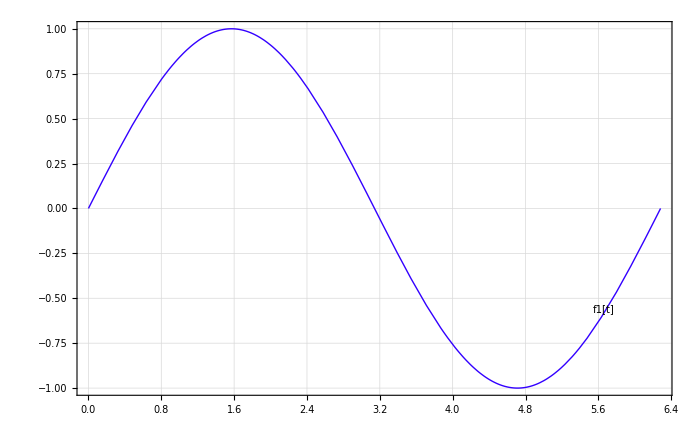

```mathematica
LabelPlot[Sin[x],{x,0,2 π},PlotStyle-> Hue[.7],CurveLabel -> {f1[t],.9}]
```

### More than one curve

As programmed here you must have the same number of curve labels as you do curves.

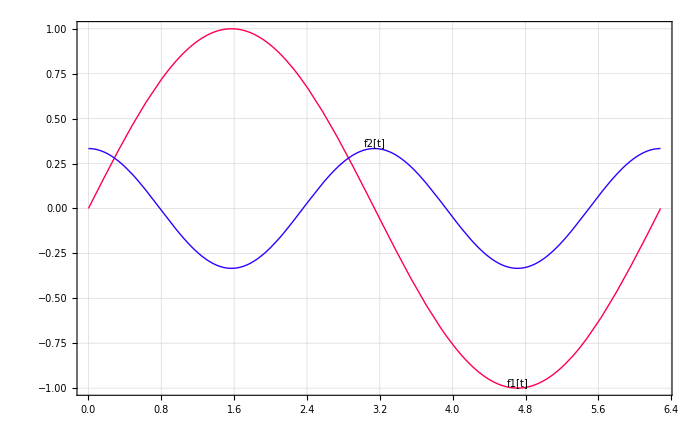

```mathematica
myplt3 = LabelPlot[{Sin[x],Cos[2 x]/3},{x,0,2 π},PlotStyle->{Hue[.95], Hue[.7]},CurveLabel ->{ {f1[t],3/4},f2[t]},PlotRange -> {{0, 2 π},{-1,1}}]
```

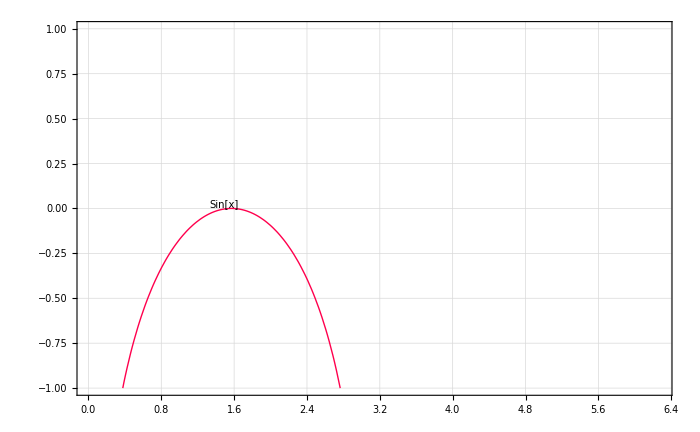

```mathematica
myplt3LL=LabelPlot[{Log[Sin[x]],Log[Cos[2x]/3]},{x,.1*Pi,2 π},PlotStyle->{Hue[.95],Hue[.7]},CurveLabel->{{Sin[x],.25},Cos[x]},PlotRange->{{0,2 π},{-1,1}}]
```

### Making changes and limitations

You can easily change the way the text appears by finding the four occurrences of StyleForm and making the appropriate changes in each. Because the labels are executed using Epilog this will not work using Show. You will only get the labels from the first plot in the Show argument.

## Calculate and plot the cross sections

Here are the actual cross section equations.  Note that the Fu and Sun technique allows direct analytical determination of the absorption cross section.

```mathematica
CScatα[a_]:=  (π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8))  ∑_(l=1)^(LastTermα[a]*2) (2 l+1)  Im[Bα[l,a]]
CAbsα[a_]:=(π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8)) ∑_(l=1)^(LastTermα[a]*2) (2 l+1) Im[Aα[l,a]]
CExtα[a_]:=(π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8)) ∑_(l=1)^(LastTermα[a]*2) (2 l+1) Im[Aα[l,a] + Bα[l,a]]
```

```mathematica
CScatβ[a_]:=  (π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8))  ∑_(l=1)^(LastTermβ[a]*2) (2 l+1)  Im[Bβ[l,a]]
CAbsβ[a_]:=(π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8)) ∑_(l=1)^(LastTermβ[a]*2) (2 l+1) Im[Aβ[l,a]]
CExtβ[a_]:=(π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8)) ∑_(l=1)^(LastTermβ[a]*2) (2 l+1) Im[Aβ[l,a] + Bβ[l,a]]
```

```mathematica
CScatγ[a_]:=  (π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermγ[a]*2) (2 l+1)  Im[Bγ[l,a]]
CAbsγ[a_]:=(π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermγ[a]*2) (2 l+1) Im[Aγ[l,a]]
CExtγ[a_]:=(π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermγ[a]*2) (2 l+1) Im[Aγ[l,a] + Bγ[l,a]]
```

```mathematica
CScatδ[a_]:=  (π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermδ[a]*2) (2 l+1)  Im[Bδ[l,a]]
CAbsδ[a_]:=(π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermδ[a]*2) (2 l+1) Im[Aδ[l,a]]
CExtδ[a_]:=(π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermδ[a]*2) (2 l+1) Im[Aδ[l,a] + Bδ[l,a]]
```

```mathematica
CScatν[a_]:=  (π a^2)/fν[a] * (π Subscript[λ, 0ν])/(2π (3* 10^8))  ∑_(l=1)^(LastTermν[a]*2) (2 l+1)  Im[Bν[l,a]]
CAbsν[a_]:=(π a^2)/fν[a] * (π Subscript[λ, 0ν])/(2π (3* 10^8)) ∑_(l=1)^(LastTermν[a]*2) (2 l+1) Im[Aν[l,a]]
CExtν[a_]:=(π a^2)/fν[a] * (π Subscript[λ, 0ν])/(2π (3* 10^8)) ∑_(l=1)^(LastTermν[a]*2) (2 l+1) Im[Aν[l,a] + Bν[l,a]]
```

```mathematica
CScatχ[a_]:=  (π a^2)/fχ[a] * (π Subscript[λ, 0χ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermχ[a]*2) (2 l+1)  Im[Bχ[l,a]]
CAbsχ[a_]:=(π a^2)/fχ[a] * (π Subscript[λ, 0χ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermχ[a]*2) (2 l+1) Im[Aχ[l,a]]
CExtχ[a_]:=(π a^2)/fχ[a] * (π Subscript[λ, 0χ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermχ[a]*2) (2 l+1) Im[Aχ[l,a] + Bχ[l,a]]
```

```mathematica
CScatζ[a_]:=  (π a^2)/fζ[a] * (π Subscript[λ, 0ζ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermζ[a]*2) (2 l+1)  Im[Bζ[l,a]]
CAbsζ[a_]:=(π a^2)/fζ[a] * (π Subscript[λ, 0ζ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermζ[a]*2) (2 l+1) Im[Aζ[l,a]]
CExtζ[a_]:=(π a^2)/fζ[a] * (π Subscript[λ, 0ζ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermζ[a]*2) (2 l+1) Im[Aζ[l,a] + Bζ[l,a]]
```

```mathematica
CScatη[a_]:=  (π a^2)/fη[a] * (π Subscript[λ, 0η])/(2π (3* 10^8))  ∑_(l=1)^(LastTermη[a]*2) (2 l+1)  Im[Bη[l,a]]
CAbsη[a_]:=(π a^2)/fη[a] * (π Subscript[λ, 0η])/(2π (3* 10^8)) ∑_(l=1)^(LastTermη[a]*2) (2 l+1) Im[Aη[l,a]]
CExtη[a_]:=(π a^2)/fη[a] * (π Subscript[λ, 0η])/(2π (3* 10^8)) ∑_(l=1)^(LastTermη[a]*2) (2 l+1) Im[Aη[l,a] + Bη[l,a]]
```

```mathematica
CScatθ[a_]:=  (π a^2)/fθ[a] * (π Subscript[λ, 0θ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermθ[a]*2) (2 l+1)  Im[Bθ[l,a]]
CAbsθ[a_]:=(π a^2)/fθ[a] * (π Subscript[λ, 0θ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermθ[a]*2) (2 l+1) Im[Aθ[l,a]]
CExtθ[a_]:=(π a^2)/fθ[a] * (π Subscript[λ, 0θ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermθ[a]*2) (2 l+1) Im[Aθ[l,a] + Bθ[l,a]]
```

```mathematica
CScatκ[a_]:=  (π a^2)/fκ[a] * (π Subscript[λ, 0κ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermκ[a]*2) (2 l+1)  Im[Bκ[l,a]]
CAbsκ[a_]:=(π a^2)/fκ[a] * (π Subscript[λ, 0κ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermκ[a]*2) (2 l+1) Im[Aκ[l,a]]
CExtκ[a_]:=(π a^2)/fκ[a] * (π Subscript[λ, 0κ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermκ[a]*2) (2 l+1) Im[Aκ[l,a] + Bκ[l,a]]
```

```mathematica
CScatμ[a_]:=  (π a^2)/fμ[a] * (π Subscript[λ, 0μ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermμ[a]*2) (2 l+1)  Im[Bμ[l,a]]
CAbsμ[a_]:=(π a^2)/fμ[a] * (π Subscript[λ, 0μ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermμ[a]*2) (2 l+1) Im[Aμ[l,a]]
CExtμ[a_]:=(π a^2)/fμ[a] * (π Subscript[λ, 0μ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermμ[a]*2) (2 l+1) Im[Aμ[l,a] + Bμ[l,a]]
```

Print out cross sections for the default parameters.

```mathematica
Print["C_Scat = ", CScatα[Subscript[r, α]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsα[Subscript[r, α]]//N," μm^2",
           "\nC_Ext = ", CExtα[Subscript[r, α]]//N," μm^2" ]
```

C_Scat = 0.135171 μm^2
C_Abs = 0.0210606 μm^2
C_Ext = 0.156231 μm^2

```mathematica
Print["C_Scat = ", CScatβ[Subscript[r, β]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsβ[Subscript[r, β]]//N," μm^2",
           "\nC_Ext = ", CExtα[Subscript[r, β]]//N," μm^2" ]
```

C_Scat = 0.127571 μm^2
C_Abs = 0.0221682 μm^2
C_Ext = 0.156231 μm^2

```mathematica
Print["C_Scat = ", CScatγ[Subscript[r, γ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsγ[Subscript[r, γ]]//N," μm^2",
           "\nC_Ext = ", CExtγ[Subscript[r, γ]]//N," μm^2" ]
```

C_Scat = 0.126098 μm^2
C_Abs = 0.0122585 μm^2
C_Ext = 0.138356 μm^2

```mathematica
Print["C_Scat = ", CScatδ[Subscript[r, δ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsδ[Subscript[r, δ]]//N," μm^2",
           "\nC_Ext = ", CExtδ[Subscript[r, δ]]//N," μm^2" ]
```

C_Scat = 0.134544 μm^2
C_Abs = 0.0121948 μm^2
C_Ext = 0.146739 μm^2

```mathematica
Print["C_Scat = ", CScatχ[Subscript[r, χ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsχ[Subscript[r, χ]]//N," μm^2",
           "\nC_Ext = ", CExtχ[Subscript[r, χ]]//N," μm^2" ]
```

C_Scat = 0.129276 μm^2
C_Abs = 0.0119599 μm^2
C_Ext = 0.141236 μm^2

```mathematica
Print["C_Scat = ", CScatζ[Subscript[r, ζ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsζ[Subscript[r, ζ]]//N," μm^2",
           "\nC_Ext = ", CExtζ[Subscript[r, ζ]]//N," μm^2" ]
```

C_Scat = 0.126453 μm^2
C_Abs = 0.0116943 μm^2
C_Ext = 0.138147 μm^2

```mathematica
Print["C_Scat = ", CScatη[Subscript[r, η]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsη[Subscript[r, η]]//N," μm^2",
           "\nC_Ext = ", CExtη[Subscript[r, η]]//N," μm^2" ]
```

C_Scat = 0.110164 μm^2
C_Abs = 0.00911305 μm^2
C_Ext = 0.119277 μm^2

```mathematica
Print["C_Scat = ", CScatθ[Subscript[r, θ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsθ[Subscript[r, θ]]//N," μm^2",
           "\nC_Ext = ", CExtθ[Subscript[r, θ]]//N," μm^2" ]
```

C_Scat = 0.104269 μm^2
C_Abs = 0.00708877 μm^2
C_Ext = 0.111358 μm^2

```mathematica
Print["C_Scat = ", CScatκ[Subscript[r, κ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsκ[Subscript[r, κ]]//N," μm^2",
           "\nC_Ext = ", CExtκ[Subscript[r, κ]]//N," μm^2" ]
```

C_Scat = 0.108389 μm^2
C_Abs = 0.00621243 μm^2
C_Ext = 0.114601 μm^2

```mathematica
Print["C_Scat = ", CScatμ[Subscript[r, μ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsμ[Subscript[r, μ]]//N," μm^2",
           "\nC_Ext = ", CExtμ[Subscript[r, μ]]//N," μm^2" ]
```

C_Scat = 0.115738 μm^2
C_Abs = 0.00607234 μm^2
C_Ext = 0.12181 μm^2

#### Linear plots of size parameter vs. cross section.

These plots take longer to generate as the size parameter increases.  Also, the multiplicative factor in the argument converts the range variable to q values rather than radius values.  This first cell sets up some default plotting parameters.

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

## Calculate and plot the efficiencies

The efficiencies are defined simply as the ratio of the cross sections to the geometrical cross sectional area of the scatterer.

```mathematica
QScatα[a_]:=  CScatα[a]/(π a^2)
QAbsα[a_]:= CAbsα[a]/(π a^2)
QExtα[a_]:=CExtα[a]/(π a^2)
```

```mathematica
QScatβ[a_]:=  CScatβ[a]/(π a^2)
QAbsβ[a_]:= CAbsβ[a]/(π a^2)
QExtβ[a_]:=CExtβ[a]/(π a^2)
```

```mathematica
QScatγ[a_]:=  CScatγ[a]/(π a^2)
QAbsγ[a_]:= CAbsγ[a]/(π a^2)
QExtγ[a_]:=CExtγ[a]/(π a^2)
```

```mathematica
QScatδ[a_]:=  CScatδ[a]/(π a^2)
QAbsδ[a_]:= CAbsδ[a]/(π a^2)
QExtδ[a_]:=CExtδ[a]/(π a^2)
```

```mathematica
QScatχ[a_]:=  CScatχ[a]/(π a^2)
QAbsχ[a_]:= CAbsχ[a]/(π a^2)
QExtχ[a_]:=CExtχ[a]/(π a^2)
```

```mathematica
QScatζ[a_]:=  CScatζ[a]/(π a^2)
QAbsζ[a_]:= CAbsζ[a]/(π a^2)
QExtζ[a_]:=CExtζ[a]/(π a^2)
```

```mathematica
QScatη[a_]:=  CScatη[a]/(π a^2)
QAbsη[a_]:= CAbsη[a]/(π a^2)
QExtη[a_]:=CExtη[a]/(π a^2)
```

```mathematica
QScatθ[a_]:=  CScatθ[a]/(π a^2)
QAbsθ[a_]:= CAbsθ[a]/(π a^2)
QExtθ[a_]:=CExtθ[a]/(π a^2)
```

```mathematica
QScatκ[a_]:=  CScatκ[a]/(π a^2)
QAbsκ[a_]:= CAbsκ[a]/(π a^2)
QExtκ[a_]:=CExtκ[a]/(π a^2)
```

```mathematica
QScatμ[a_]:=  CScatμ[a]/(π a^2)
QAbsμ[a_]:= CAbsμ[a]/(π a^2)
QExtμ[a_]:=CExtμ[a]/(π a^2)
```

Print out efficiencies for the default parameters.

```mathematica
Print["Q_Scatα = ",QScatα[Subscript[r, α]]//N,"\nQ_Absα = ",QAbsα[Subscript[r, α]]//N,"\nQ_Extα= ",QExtα[Subscript[r, α]]//N ]
```

Q_Scatα = 4.30262
Q_Absα = 0.670381
Q_Extα= 4.973

```mathematica
Print["Q_Scatβ = ",QScatβ[Subscript[r, β]]//N,"\nQ_Absβ = ",QAbsβ[Subscript[r, β]]//N,"\nQ_Extβ = ",QExtβ[Subscript[r, β]]//N ]
```

Q_Scatβ = 4.06072
Q_Absβ = 0.705634
Q_Extβ = 4.76636

```mathematica
Print["Q_Scatγ = ",QScatγ[Subscript[r, γ]]//N,"\nQ_Absγ = ",QAbsγ[Subscript[r, γ]]//N,"\nQ_Extγ = ",QExtγ[Subscript[r, γ]]//N ]
```

Q_Scatγ = 4.01382
Q_Absγ = 0.390201
Q_Extγ = 4.40402

```mathematica
Print["Q_Scatδ = ",QScatδ[Subscript[r, δ]]//N,"\nQ_Absδ = ",QAbsδ[Subscript[r, δ]]//N,"\nQ_Extδ = ",QExtδ[Subscript[r, δ]]//N ]
```

Q_Scatδ = 4.28268
Q_Absδ = 0.388172
Q_Extδ = 4.67086

```mathematica
Print["Q_Scatϵ = ",QScatϵ[Subscript[r, ϵ]]//N,"\nQ_Absϵ = ",QAbsϵ[Subscript[r, ϵ]]//N,"\nQ_(Ext ϵ) = ",QExtϵ[Subscript[r, ϵ]]//N ]
```

Q_Scatϵ = QScatϵ[r_ϵ]
Q_Absϵ = QAbsϵ[r_ϵ]
Q_(Ext ϵ) = QExtϵ[r_ϵ]

#### Linear plots of size parameter vs. efficiency.

Note that these plots take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

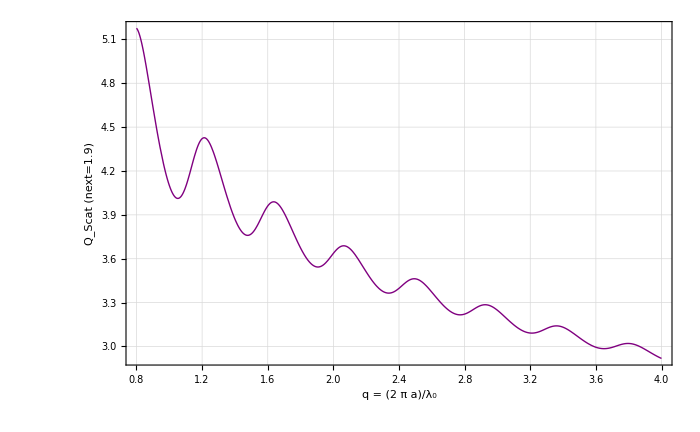

```mathematica
QScatPlot = Plot[{QScatα[i Subscript[λ, 0α]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.9)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

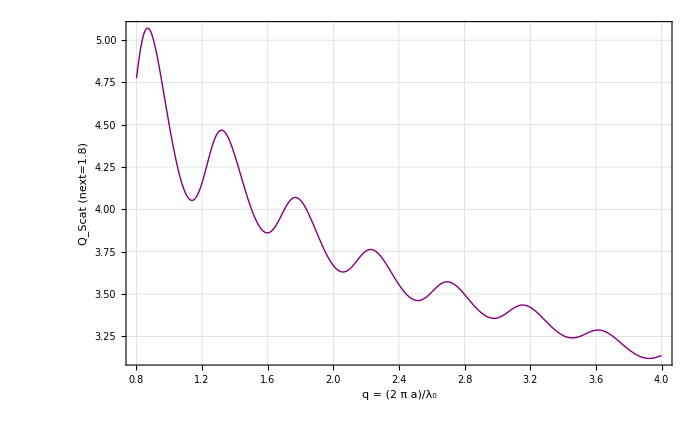

```mathematica
Plot[{QScatβ[i Subscript[λ, 0β]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.8)"}]
```

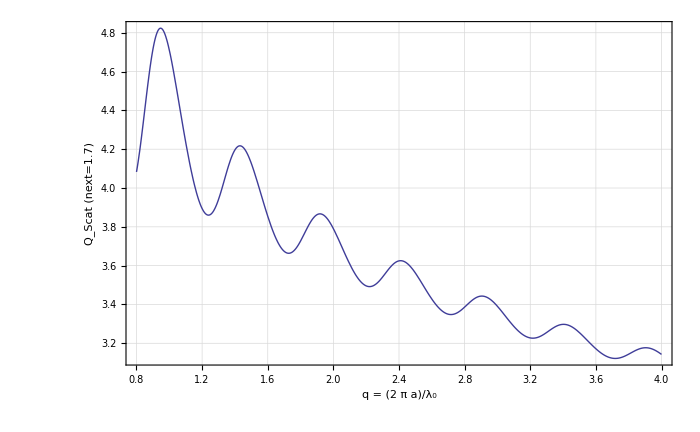

```mathematica
Plot[{QScatγ[i Subscript[λ, 0γ]/(2π)],}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.7)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

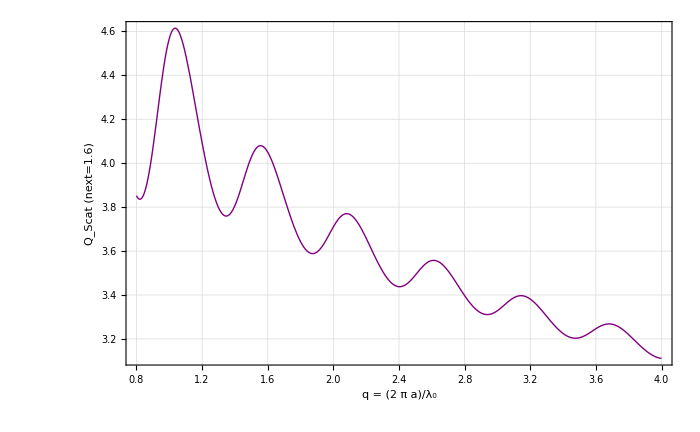

```mathematica
Plot[{QScatδ[i Subscript[λ, 0δ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.6)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

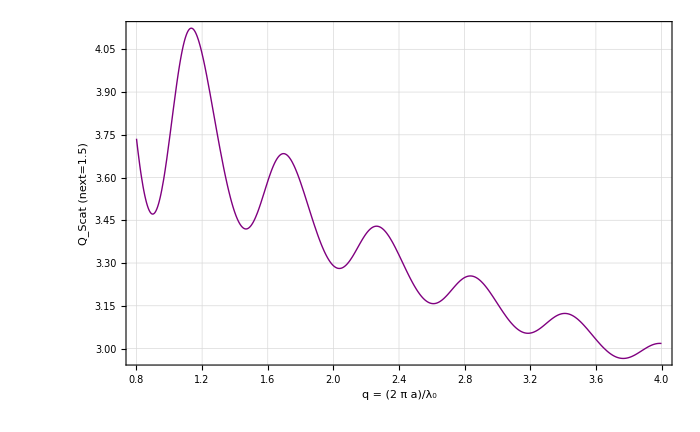

```mathematica
Plot[{QScatχ[i Subscript[λ, 0χ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.5)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

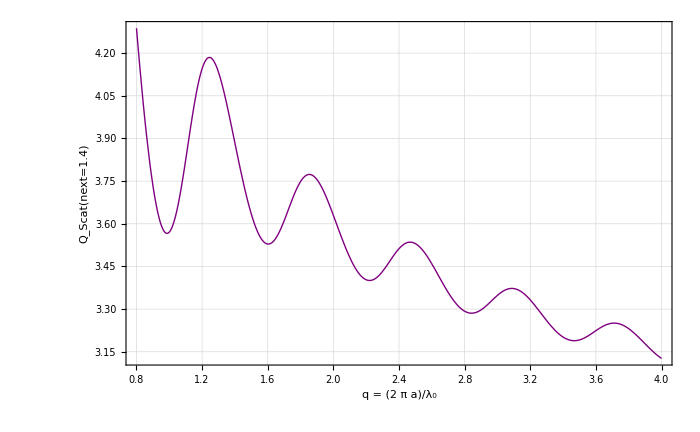

```mathematica
Plot[{QScatζ[i Subscript[λ, 0ζ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat(next=1.4)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

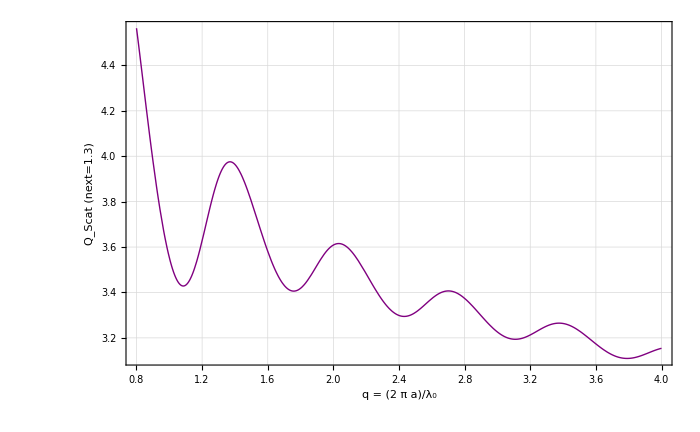

```mathematica
Plot[{QScatη[i Subscript[λ, 0η]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.3)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

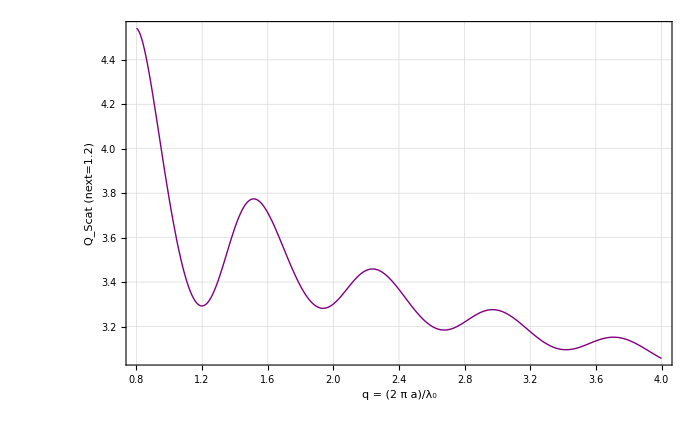

```mathematica
Plot[{QScatθ[i Subscript[λ, 0θ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.2)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

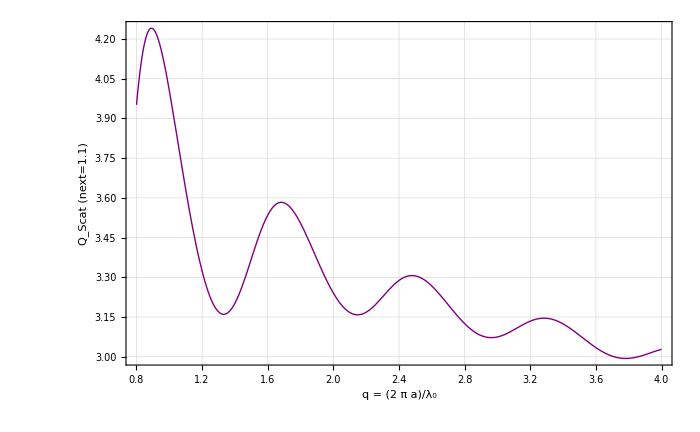

```mathematica
Plot[{QScatκ[i Subscript[λ, 0κ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.1)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

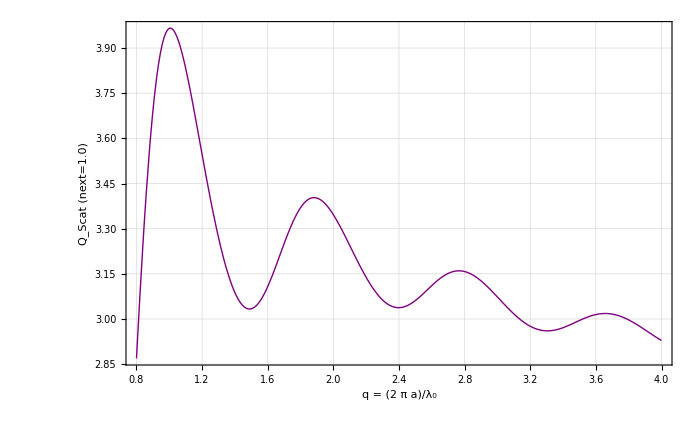

```mathematica
Plot[{QScatμ[i Subscript[λ, 0μ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.0)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

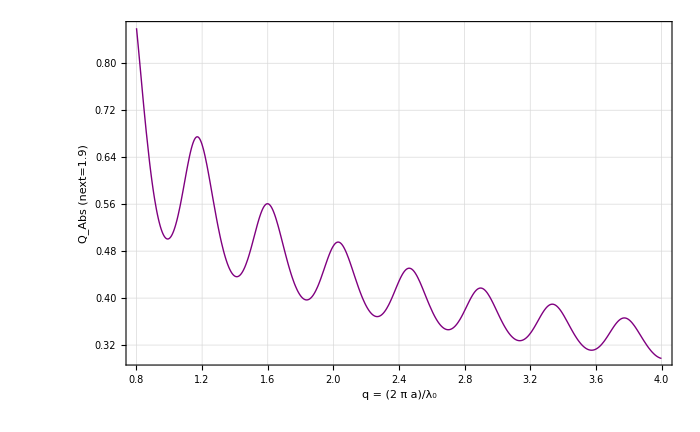

```mathematica
QScatPlot = Plot[{QAbsα[i Subscript[λ, 0α]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.9)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

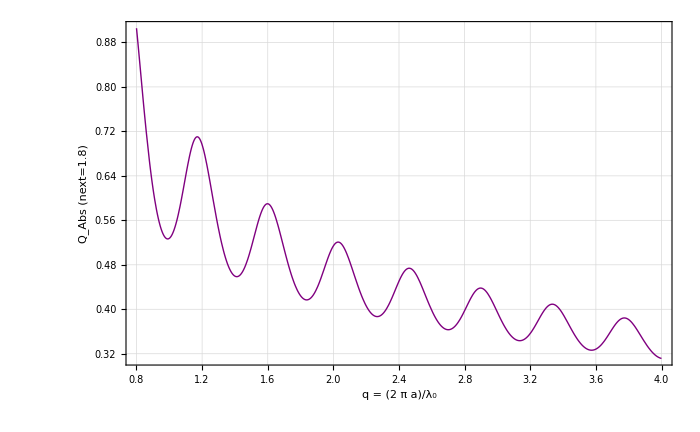

```mathematica
Plot[{QAbsβ[i Subscript[λ, 0β]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.8)"}]
```

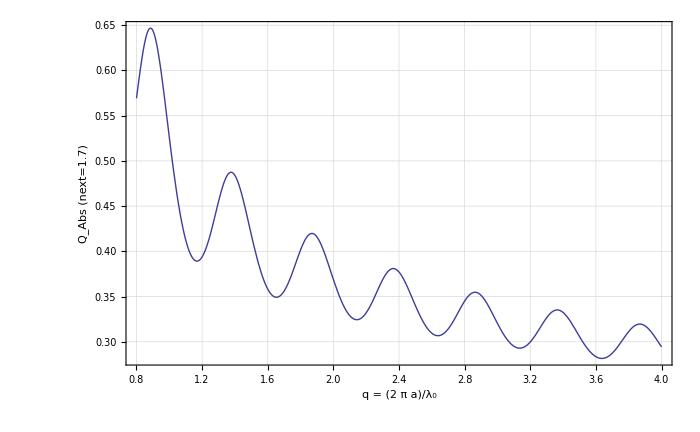

```mathematica
Plot[{QAbsγ[i Subscript[λ, 0γ]/(2π)],}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.7)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

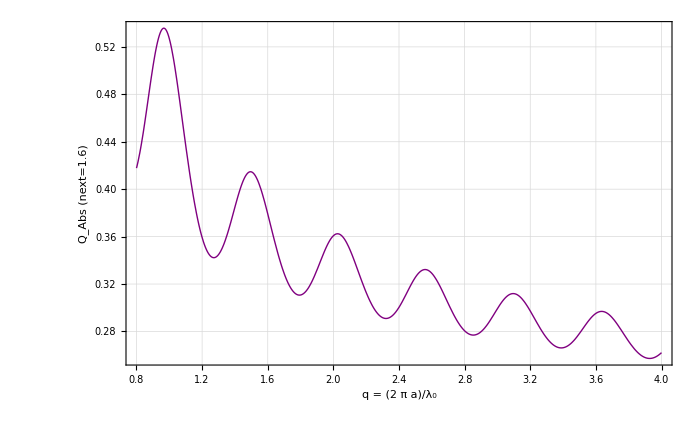

```mathematica
Plot[{QAbsδ[i Subscript[λ, 0δ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.6)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

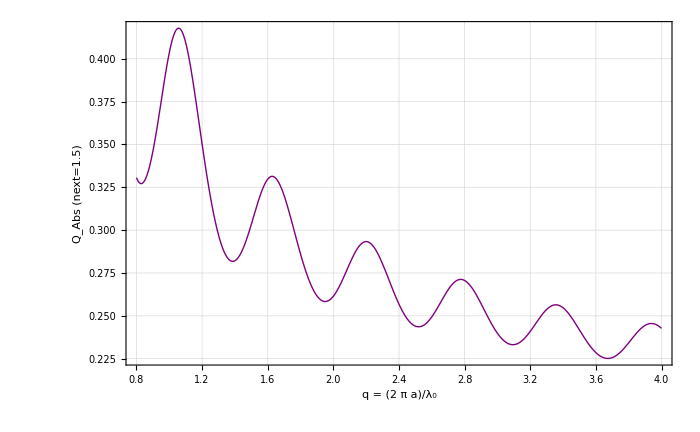

```mathematica
Plot[{QAbsχ[i Subscript[λ, 0χ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.5)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

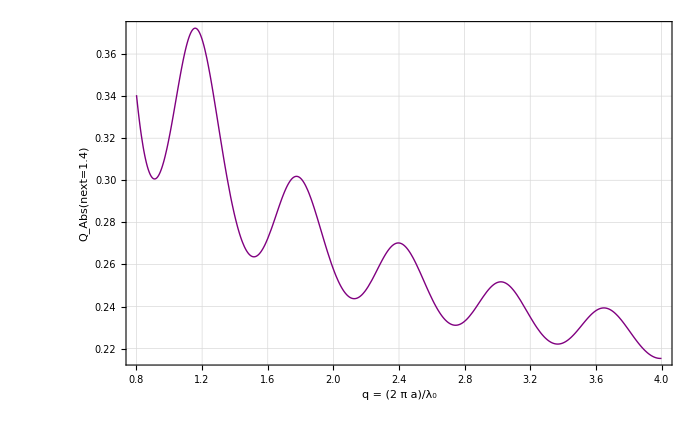

```mathematica
Plot[{QAbsζ[i Subscript[λ, 0ζ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs(next=1.4)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

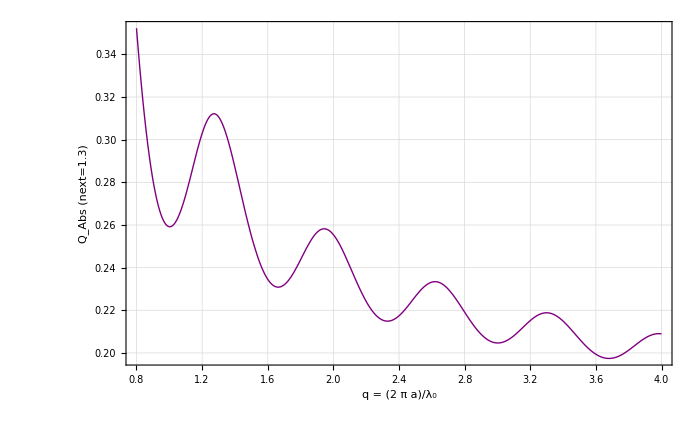

```mathematica
Plot[{QAbsη[i Subscript[λ, 0η]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.3)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

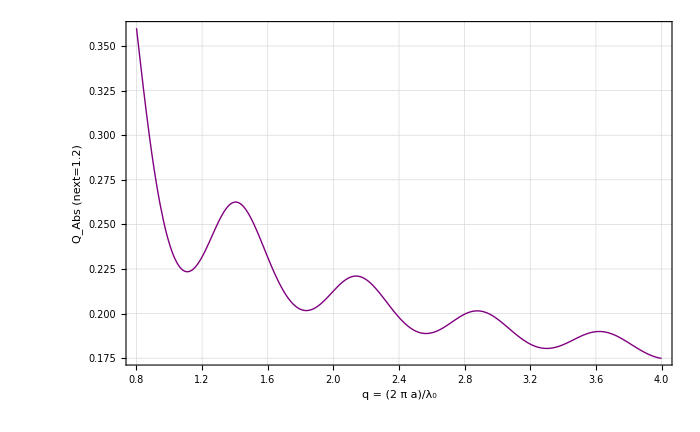

```mathematica
Plot[{QAbsθ[i Subscript[λ, 0θ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.2)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

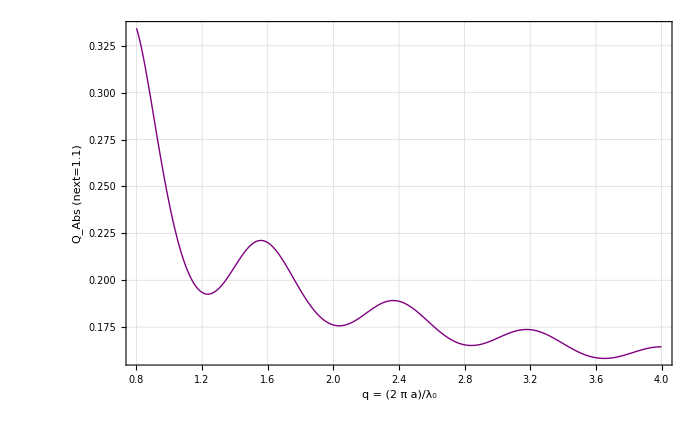

```mathematica
Plot[{QAbsκ[i Subscript[λ, 0κ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.1)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

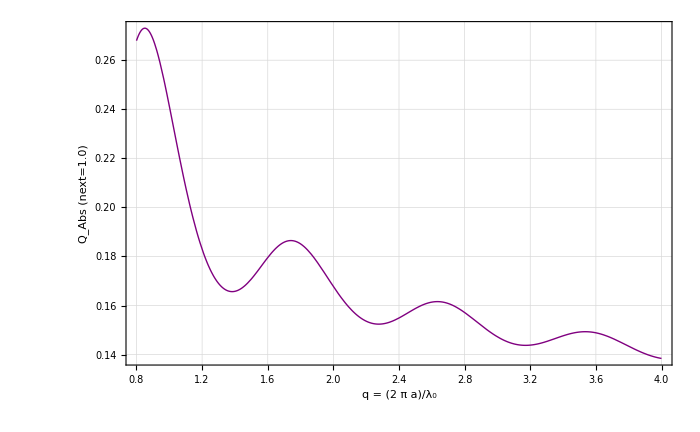

```mathematica
Plot[{QAbsμ[i Subscript[λ, 0μ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs (next=1.0)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

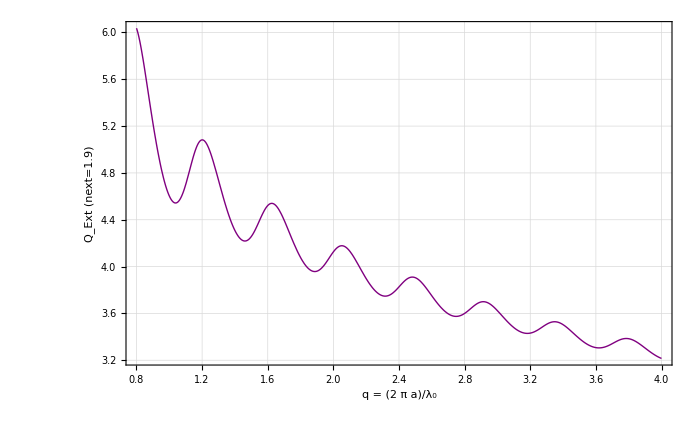

```mathematica
QScatPlot = Plot[{QExtα[i Subscript[λ, 0α]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.9)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

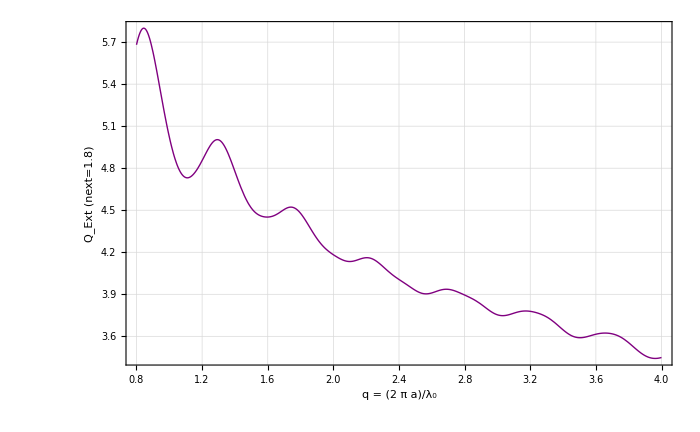

```mathematica
Plot[{QExtβ[i Subscript[λ, 0β]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.8)"}]
```

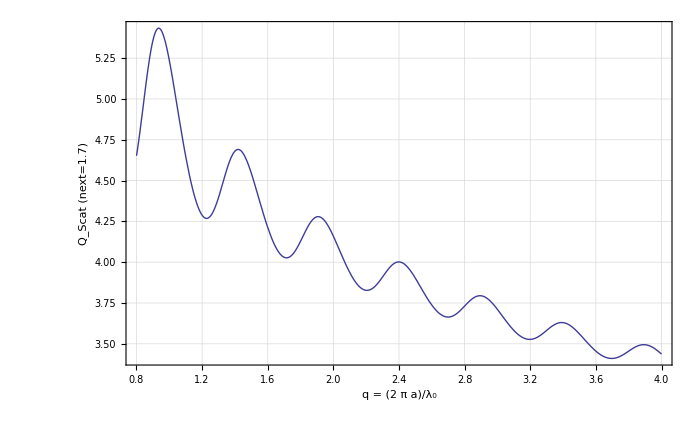

```mathematica
Plot[{QExtγ[i Subscript[λ, 0γ]/(2π)],}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat (next=1.7)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

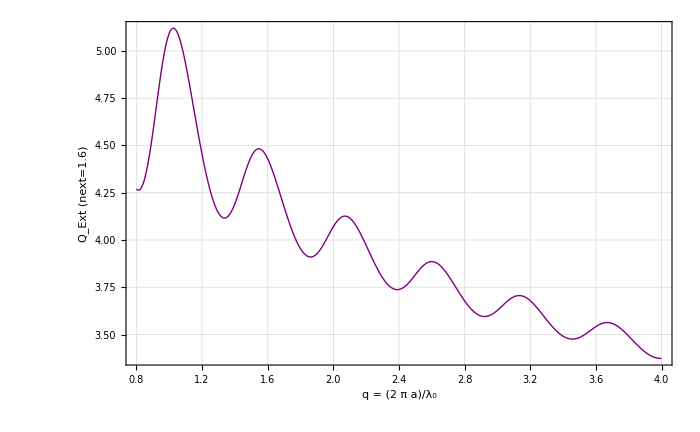

```mathematica
Plot[{QExtδ[i Subscript[λ, 0δ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.6)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

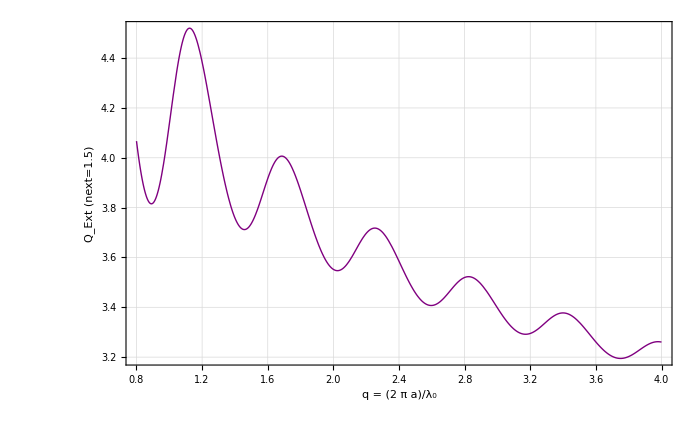

```mathematica
Plot[{QExtχ[i Subscript[λ, 0χ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.5)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

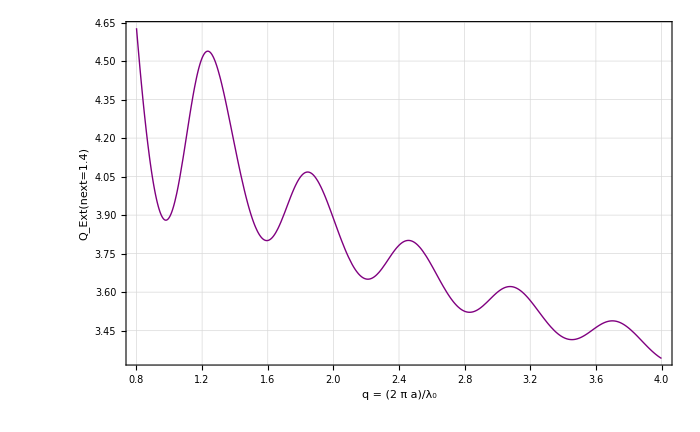

```mathematica
Plot[{QExtζ[i Subscript[λ, 0ζ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext(next=1.4)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

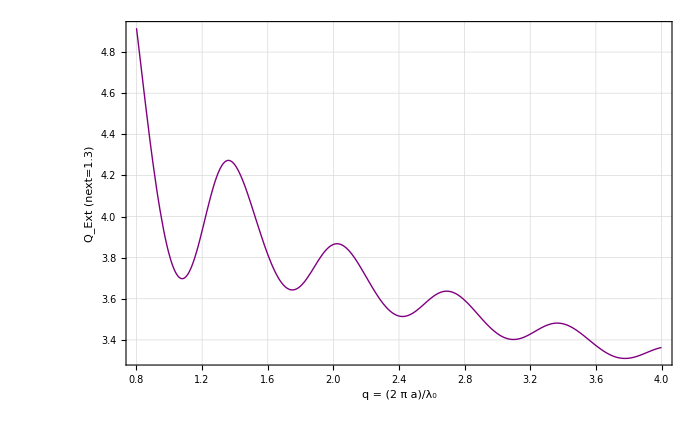

```mathematica
Plot[{QExtη[i Subscript[λ, 0η]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.3)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

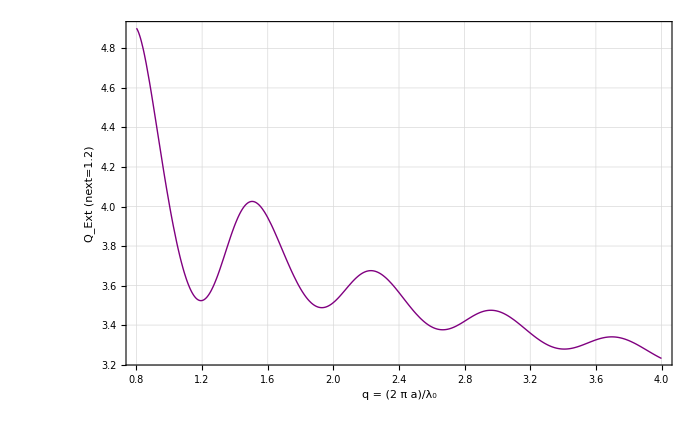

```mathematica
Plot[{QExtθ[i Subscript[λ, 0θ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.2)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

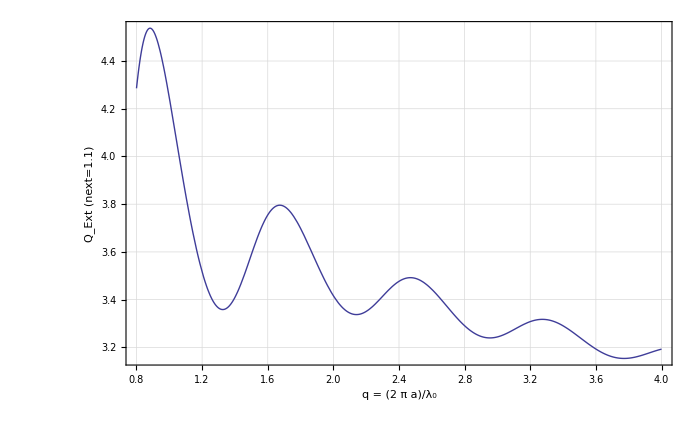

```mathematica
Plot[{QExtκ[i Subscript[λ, 0κ]/(2π)]}, {i,.8, 4},PlotStyle->{Automatic},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.1)"}]
```

Graphics::gprim: Automatic was encountered where a Graphics primitive or directive was expected.

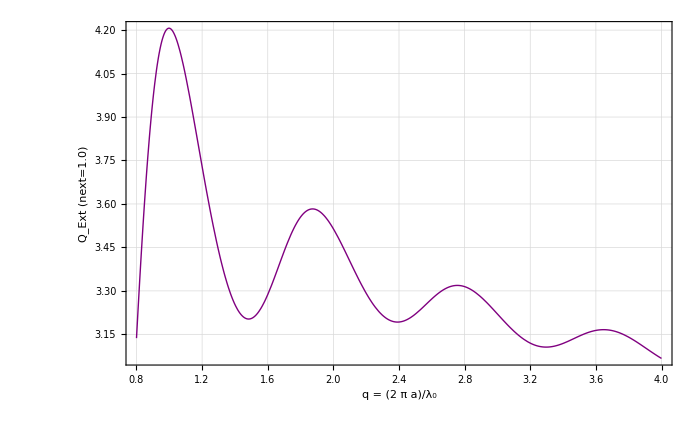

```mathematica
Plot[{QExtμ[i Subscript[λ, 0μ]/(2π)]}, {i,.8, 4},PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext (next=1.0)"}]
```

## Calculate and plot the asymmetry factor

The equation for the asymmetry factor comes from Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001, pp. 1354-1361).

```mathematica
gα[a_] := (2∑_(l=1)^LastTermα[a] ((l(l+2))/(l + 1) Re[(anα[l,a]*  SuperStar[anα[l+1,a]]+ bnα[l,a]*SuperStar[bnα[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anα[l,a] *SuperStar[bnα[l,a]])]))/(∑_(l=1)^LastTermα[a] (2l+1)((Abs[anα[l,a]])^2 + (Abs[bnα[l,a]])^2))
```

```mathematica
gβ[a_] := (2∑_(l=1)^LastTermβ[a] ((l(l+2))/(l + 1) Re[(anβ[l,a]*  SuperStar[anβ[l+1,a]]+ bnβ[l,a]*SuperStar[bnβ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anβ[l,a] *SuperStar[bnβ[l,a]])]))/(∑_(l=1)^LastTermβ[a] (2l+1)((Abs[anβ[l,a]])^2 + (Abs[bnβ[l,a]])^2))
```

```mathematica
gγ[a_] := (2∑_(l=1)^LastTermγ[a] ((l(l+2))/(l + 1) Re[(anγ[l,a]*  SuperStar[anγ[l+1,a]]+ bnγ[l,a]*SuperStar[bnγ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anγ[l,a] *SuperStar[bnγ[l,a]])]))/(∑_(l=1)^LastTermγ[a] (2l+1)((Abs[anγ[l,a]])^2 + (Abs[bnγ[l,a]])^2))
```

```mathematica
gδ[a_] := (2∑_(l=1)^LastTermδ[a] ((l(l+2))/(l + 1) Re[(anδ[l,a]*  SuperStar[anδ[l+1,a]]+ bnδ[l,a]*SuperStar[bnδ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anδ[l,a] *SuperStar[bnδ[l,a]])]))/(∑_(l=1)^LastTermδ[a] (2l+1)((Abs[anδ[l,a]])^2 + (Abs[bnδ[l,a]])^2))
```

```mathematica
gχ[a_] := (2∑_(l=1)^LastTermχ[a] ((l(l+2))/(l + 1) Re[(anχ[l,a]*  SuperStar[anχ[l+1,a]]+ bnχ[l,a]*SuperStar[bnχ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anχ[l,a] *SuperStar[bnχ[l,a]])]))/(∑_(l=1)^LastTermχ[a] (2l+1)((Abs[anχ[l,a]])^2 + (Abs[bnχ[l,a]])^2))
```

```mathematica
gν[a_] := (2∑_(l=1)^LastTermν[a] ((l(l+2))/(l + 1) Re[(anν[l,a]*  SuperStar[anν[l+1,a]]+ bnν[l,a]*SuperStar[bnν[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anν[l,a] *SuperStar[bnν[l,a]])]))/(∑_(l=1)^LastTermν[a] (2l+1)((Abs[anν[l,a]])^2 + (Abs[bnν[l,a]])^2))
```

```mathematica
gζ[a_] := (2 ∑_(l=1)^LastTermζ[a] ((l(l+2))/(l + 1) Re[(anζ[l,a]*  SuperStar[anζ[l+1,a]]+ bnζ[l,a]*SuperStar[bnζ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anζ[l,a] *SuperStar[bnζ[l,a]])]))/(∑_(l=1)^LastTermζ[a] (2l+1)((Abs[anζ[l,a]])^2 + (Abs[bnζ[l,a]])^2))
```

```mathematica
gη[a_] := (2 ∑_(l=1)^LastTermη[a] ((l(l+2))/(l + 1) Re[(anη[l,a]*  SuperStar[anη[l+1,a]]+ bnη[l,a]*SuperStar[bnη[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anη[l,a] *SuperStar[bnη[l,a]])]))/(∑_(l=1)^LastTermη[a] (2l+1)((Abs[anη[l,a]])^2 + (Abs[bnη[l,a]])^2))
```

```mathematica
gθ[a_] := (2 ∑_(l=1)^LastTermθ[a] ((l(l+2))/(l + 1) Re[(anθ[l,a]*  SuperStar[anθ[l+1,a]]+ bnθ[l,a]*SuperStar[bnθ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anθ[l,a] *SuperStar[bnθ[l,a]])]))/(∑_(l=1)^LastTermθ[a] (2l+1)((Abs[anθ[l,a]])^2 + (Abs[bnθ[l,a]])^2))
```

```mathematica
gκ[a_] := (2 ∑_(l=1)^LastTermκ[a] ((l(l+2))/(l + 1) Re[(anκ[l,a]*  SuperStar[anκ[l+1,a]]+ bnκ[l,a]*SuperStar[bnκ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anκ[l,a] *SuperStar[bnκ[l,a]])]))/(∑_(l=1)^LastTermκ[a] (2l+1)((Abs[anκ[l,a]])^2 + (Abs[bnκ[l,a]])^2))
```

```mathematica
gμ[a_] := (2 ∑_(l=1)^LastTermμ[a] ((l(l+2))/(l + 1) Re[(anμ[l,a]*  SuperStar[anμ[l+1,a]]+ bnμ[l,a]*SuperStar[bnμ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anμ[l,a] *SuperStar[bnμ[l,a]])]))/(∑_(l=1)^LastTermμ[a] (2l+1)((Abs[anμ[l,a]])^2 + (Abs[bnμ[l,a]])^2))
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gα[Subscript[r, α]]//N]]
```

The anisotropy value is g = 0.471659

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gβ[Subscript[r, β]]//N]]
```

The anisotropy value is g = 0.413752

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gγ[Subscript[r, γ]]//N]]
```

The anisotropy value is g = 0.382319

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gδ[Subscript[r, δ]]//N]]
```

The anisotropy value is g = 0.396522

#### Create plot of size parameter vs. asymmetry factor.

```mathematica
The assummetry factor denotes the symmetry of the phase function and related whether forward scattering or back scattering is dominant (greater than .5 is forward, less than .5 is backscattering).
```

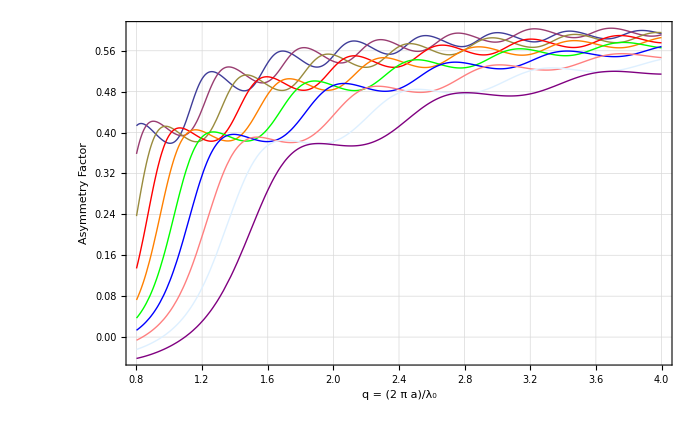

```mathematica
gPlot = Plot[{gα[i Subscript[λ, 0α]/(2π)],gβ[i Subscript[λ, 0β]/(2π)],gγ[i Subscript[λ, 0γ]/(2π)],gδ[i Subscript[λ, 0δ]/(2π)],gχ[i Subscript[λ, 0χ]/(2π)],gζ[i Subscript[λ, 0ζ]/(2π)],gη[i Subscript[λ, 0η]/(2π)],gθ[i Subscript[λ, 0θ]/(2π)],gκ[i Subscript[λ, 0κ]/(2π)],gμ[i Subscript[λ, 0μ]/(2π)]}, {i,.8, 4}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"}]
```

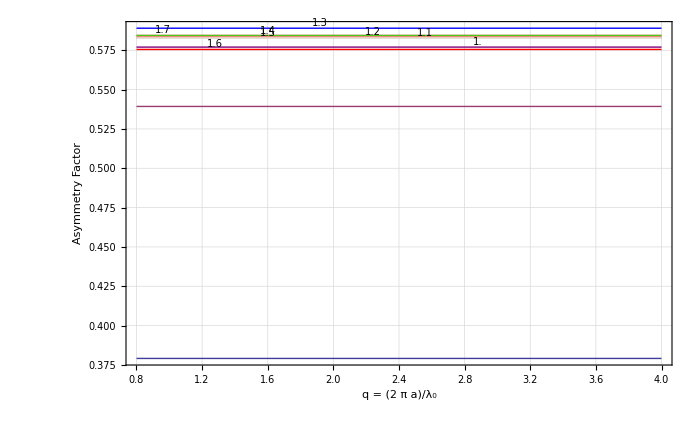

```mathematica
GLabelPlot= LabelPlot[{gα[i Subscript[λ, 0α]/(2π)],gβ[i Subscript[λ, 0β]/(2π)],gγ[i Subscript[λ, 0γ]/(2π)],gδ[i Subscript[λ, 0δ]/(2π)],gχ[i Subscript[λ, 0χ]/(2π)],gζ[i Subscript[λ, 0ζ]/(2π)],gη[i Subscript[λ, 0η]/(2π)],gθ[i Subscript[λ, 0θ]/(2π)],gκ[i Subscript[λ, 0κ]/(2π)],gμ[i Subscript[λ, 0μ]/(2π)]}, {i,.8, 4}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"},CurveLabel->{{next=1.9,.1},{next=1.8,.2},{next=1.7,.3},{next=1.6,.4},{next=1.5,.5},{next=1.4,.5},{next=1.3,.6},{next=1.2,.7},{next=1.1,.8},{next=1.0,.9}}]
```

## Calculate and plot the albedo

The albedo is simply the ratio of the scattering to extinction cross sections.

```mathematica
albedoα[a_] := CScatα[a]/CExtα[a];
StringJoin["The albedo is ", ToString[albedoα[Subscript[r, α]]//N]]
```

The albedo is 0.865196

```mathematica
albedoβ[a_] := CScatβ[a]/CExtβ[a];
StringJoin["The albedo is ", ToString[albedoβ[Subscript[r, β]]//N]]
```

The albedo is 0.851955

```mathematica
albedoγ[a_] := CScatγ[a]/CExtγ[a];
StringJoin["The albedo is ", ToString[albedoγ[Subscript[r, γ]]//N]]
```

The albedo is 0.911399

```mathematica
albedoδ[a_] := CScatδ[a]/CExtδ[a];
StringJoin["The albedo is ", ToString[albedoδ[Subscript[r, δ]]//N]]
```

The albedo is 0.916895

```mathematica
albedoχ[a_] := CScatχ[a]/CExtχ[a];
```

```mathematica
albedoζ[a_] := CScatζ[a]/CExtζ[a];
StringJoin["The albedo is ", ToString[albedoζ[Subscript[r, ζ]]//N]]
```

The albedo is 0.915349

```mathematica
albedoη[a_] := CScatη[a]/CExtη[a];
```

```mathematica
albedoζ[a_] := CScatθ[a]/CExtθ[a];
```

```mathematica
albedoκ[a_] := CScatκ[a]/CExtκ[a];
```

```mathematica
albedoμ[a_] := CScatμ[a]/CExtμ[a];
```

```mathematica
Manipulate[N[albedo[i*Subscript[λ, 0]/(2π)],3],{i,1,6}]
```

#### Create plot of albedo vs. size parameter.

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* In the next section of code, i is the size paramater.  *)
```

```mathematica
AlbedoPlot = LogLinearPlot[{albedoα[i Subscript[λ, 0α]/(2π)],albedoβ[i Subscript[λ, 0β]/(2π)],albedoγ[i Subscript[λ, 0γ]/(2π)],albedoδ[i Subscript[λ, 0δ]/(2π)],albedoχ[i (Subscript[λ, 0] χ)/(2π)],albedoζ[i Subscript[λ, 0ζ]/(2π)],albedoη[i Subscript[λ, 0η]/(2π)],albedoθ[i Subscript[λ, 0θ]/(2π)],albedoκ[i Subscript[λ, 0κ]/(2π)],albedoμ[i Subscript[λ, 0μ]/(2π)]}, {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"}]
```

$Aborted

```mathematica
AlbedoLabelPlot=LabelPlot[{albedoα[i Subscript[λ, 0α]/(2π)],albedoβ[i Subscript[λ, 0β]/(2π)],albedoγ[i Subscript[λ, 0γ]/(2π)],albedoδ[i Subscript[λ, 0δ]/(2π)],albedoχ[i Subscript[λ, 0χ]/(2π)],albedoζ[i Subscript[λ, 0ζ]/(2π)],albedoη[i Subscript[λ, 0η]/(2π)],albedoθ[i Subscript[λ, 0θ]/(2π)],albedoκ[i Subscript[λ, 0κ]/(2π)],albedoμ[i Subscript[λ, 0μ]/(2π)]}, {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"},CurveLabel->{{next=1.9,.1},{next=1.8,.2},{next=1.7,.3},{next=1.6,.4},{next=1.5,.5},{next=1.4,.5},{next=1.3,.6},{next=1.2,.7},{next=1.1,.8},{next=1.0,.9}}]
```

```mathematica
AlbedoLabelPlot=LabelPlot[{Log[albedoα[i Subscript[λ, 0α]/(2π)]],Log[albedoβ[i Subscript[λ, 0β]/(2π)]],Log[albedoγ[i Subscript[λ, 0γ]/(2π)]],Log[albedoδ[i Subscript[λ, 0δ]/(2π)]],Log[albedoχ[i Subscript[λ, 0χ]/(2π)]],Log[albedoζ[i Subscript[λ, 0ζ]/(2π)]],Log[albedoη[i Subscript[λ, 0η]/(2π)]],Log[albedoθ[i Subscript[λ, 0θ]/(2π)]],Log[albedoκ[i Subscript[λ, 0κ]/(2π)]],Log[albedoμ[i Subscript[λ, 0μ]/(2π)]]}, {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Thin,Automatic,Red,Orange,Green,Blue,Pink,LightBlue,Purple}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"},CurveLabel->{{next=1.9,.1},{next=1.8,.2},{next=1.7,.3},{next=1.6,.4},{next=1.5,.5},{next=1.4,.5},{next=1.3,.6},{next=1.2,.7},{next=1.1,.8},{next=1.0,.9}}]
```